### Semi-fusing strings

(all strings except the maximal string is fused; mode numbers are chosen to be maximal with the standard way of constructing rigged configurations)

NOTES on functions: 
1. SolutionFromModeConfiguration[modes,length] is the function I call to find string solutions (in StringSolver). From this function, sol[1] is a list of centres of strings and is the object I use.

2. log[x,branch choice, branch cut] is listed in StringSolver

3. Note that I take v[a,s,k]->-v[a,s,k] before putting in numbers from sol[1] from StringSolver. This is due to StringSolver and WronskianSolver using different conventions.

4. SolutionSYTW[SYT] is the function I call from WronskianSolver to get exact solutions as a list of c coefficients (I store as exactsol=SolutionSYTW[SYT] where exactsol[[-1,-1]] is the final list of c coefficients; exactsol[[-2,-1]] is the second final; and so on).

#### String configuration {2,2} for YD={4,4}

```mathematica
rigged={{lboxes={1,1,1,1,1,1,1,1}},{{2,2},{}},{{0,0},{}}};
%//showRC
SolutionFromModeConfiguration[modes=(rigged//RiggedToModes),L=lboxes//Length];
```

-Graphics- | ∅

```mathematica
thetarels22={((x[1,1]-Λ+I/2)/(x[1,1]-Λ-I/2))((x[1,1]+I/2)/(x[1,1]-I/2))^ll-(x[1,1]-x[1,3]+I)/(x[1,1]-x[1,3]-I)(x[1,1]-x[1,4]+I)/(x[1,1]-x[1,4]-I)(x[1,1]-x[1,2]+I)/(x[1,1]-x[1,2]-I),((x[1,2]-Λ+I/2)/(x[1,2]-Λ-I/2))((x[1,2]+I/2)/(x[1,2]-I/2))^ll-(x[1,2]-x[1,3]+I)/(x[1,2]-x[1,3]-I)(x[1,2]-x[1,4]+I)/(x[1,2]-x[1,4]-I)(x[1,2]-x[1,1]+I)/(x[1,2]-x[1,1]-I),((x[1,4]-Λ+I/2)/(x[1,4]-Λ-I/2))((x[1,4]+I/2)/(x[1,4]-I/2))^ll((x[1,3]-Λ+I/2)/(x[1,3]-Λ-I/2))((x[1,3]+I/2)/(x[1,3]-I/2))^ll-(x[1,3]-x[1,2]+I)/(x[1,3]-x[1,2]-I)(x[1,3]-x[1,1]+I)/(x[1,3]-x[1,1]-I)(x[1,4]-x[1,2]+I)/(x[1,4]-x[1,2]-I)(x[1,4]-x[1,1]+I)/(x[1,4]-x[1,1]-I)}/.x[1,4]->v[2]-I/2/.x[1,3]->v[2]+I/2;
```

```mathematica
vars22={x[1,1],x[1,2],v[2]};
```

```mathematica
δ=-10^-10I+10^-4;
predictor=initpredictor={x[1,1]->v[1,2,1]+0.5I-δ,x[1,2]->v[1,2,1]-0.5I+δ,v[2]->v[1,2,2]}/.sol[1];
initpredictor
FindRoot[thetarels22/.ll->7/.Λ->0,{vars22,vars22/.initpredictor}//Transpose,WorkingPrecision->20,MaxIterations->1000]
```

{x[1,1]→0.471072+0.5 ⅈ,x[1,2]→0.471272-0.5 ⅈ,v[2]→-0.4711719514470233524110542308503534391972}

{x[1,1]→0.46466812836603021675+0.50232710460871735554 ⅈ,x[1,2]→0.46466812836603021675-0.50232710460871735554 ⅈ,v[2]→-0.46968788307307112486-9.3661096471064664309×10^-32 ⅈ}

```mathematica
ThetaSols={};
Thetas={};
predictor=initpredictor;
Do[
minsolrep=FindRoot[thetarels22/.ll->i/.Λ->0,{vars22,vars22/.predictor}//Transpose,WorkingPrecision->20,MaxIterations->1000];AppendTo[ThetaSols,minsolrep];AppendTo[Thetas,i];predictor=minsolrep;,{i,7,20,1/2}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

General::stop: Further output of FindRoot::sszero will be suppressed during this calculation.

```mathematica
ThetaSols={};
Thetas={};
predictor=initpredictor;
Do[
minsolrep=FindRoot[thetarels22/.Λ->i,{vars22,vars22/.predictor}//Transpose,WorkingPrecision->20,MaxIterations->1000];AppendTo[ThetaSols,minsolrep];AppendTo[Thetas,i];predictor=minsolrep;,{i,0,10,1/50}]
```

{0.471072+0.5 ⅈ,0.471272-0.5 ⅈ,-0.471172}

{0.464668+0.502327 ⅈ,0.464668-0.502327 ⅈ,-0.469688-9.36611×10^-32 ⅈ}

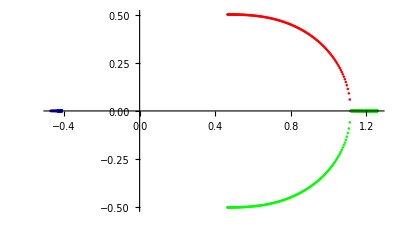

```mathematica
initpredictor//Values//N
ThetaSols[[1]]//Values//N

ComplexListPlot[{initpredictor//Values,ThetaSols[[All,1]]//Values,ThetaSols[[All,2]]//Values,ThetaSols[[All,3]]//Values},PlotRange->All,PlotStyle->{Orange,Red,Green,Blue}]
```

#### String configuration {3,2} where the 3-string is maximal for YD={5,5}

```mathematica
rigged={{lboxes={1,1,1,1,1,1,1,1,1,1}},{{3,2},{}},{{0,1},{0},{}}};
%//showRC
SolutionFromModeConfiguration[modes=(rigged//RiggedToModes),L=lboxes//Length];
```

-Graphics- | ∅

```mathematica
thetarels32={((x[1,1]-Λ+I/2)/(x[1,1]-Λ-I/2))((x[1,1]+I/2)/(x[1,1]-I/2))^9-(x[1,1]-x[1,3]+I)/(x[1,1]-x[1,3]-I)(x[1,1]-x[1,4]+I)/(x[1,1]-x[1,4]-I)(x[1,1]-x[1,2]+I)/(x[1,1]-x[1,2]-I)(x[1,1]-x[1,5]+I)/(x[1,1]-x[1,5]-I),((x[1,2]-Λ+I/2)/(x[1,2]-Λ-I/2))((x[1,2]+I/2)/(x[1,2]-I/2))^9-(x[1,2]-x[1,3]+I)/(x[1,2]-x[1,3]-I)(x[1,2]-x[1,4]+I)/(x[1,2]-x[1,4]-I)(x[1,2]-x[1,1]+I)/(x[1,2]-x[1,1]-I)(x[1,2]-x[1,5]+I)/(x[1,2]-x[1,5]-I),((x[1,3]-Λ+I/2)/(x[1,3]-Λ-I/2))((x[1,3]+I/2)/(x[1,3]-I/2))^9-(x[1,3]-x[1,1]+I)/(x[1,3]-x[1,1]-I)(x[1,3]-x[1,2]+I)/(x[1,3]-x[1,2]-I)(x[1,3]-x[1,4]+I)/(x[1,3]-x[1,4]-I)(x[1,3]-x[1,5]+I)/(x[1,3]-x[1,5]-I),((x[1,4]-Λ+I/2)/(x[1,4]-Λ-I/2))((x[1,4]+I/2)/(x[1,4]-I/2))^9((x[1,5]-Λ+I/2)/(x[1,5]-Λ-I/2))((x[1,5]+I/2)/(x[1,5]-I/2))^9-(x[1,5]-x[1,2]+I)/(x[1,5]-x[1,2]-I)(x[1,5]-x[1,1]+I)/(x[1,5]-x[1,1]-I)(x[1,5]-x[1,3]+I)/(x[1,5]-x[1,3]-I)(x[1,4]-x[1,2]+I)/(x[1,4]-x[1,2]-I)(x[1,4]-x[1,3]+I)/(x[1,4]-x[1,3]-I)(x[1,4]-x[1,1]+I)/(x[1,4]-x[1,1]-I)}/.x[1,4]->v[2]-I/2/.x[1,5]->v[2]+I/2;
```

```mathematica
numthetarels32={(ⅈ/2+x[1,1])^9 (ⅈ/2-Λ+x[1,1])((-ⅈ+x[1,1]-x[1,2]) (-ⅈ+x[1,1]-x[1,3]) (-ⅈ+x[1,1]-x[1,4]) (-ⅈ+x[1,1]-x[1,5]))-Exp[2Pi I t1]((ⅈ+x[1,1]-x[1,2]) (ⅈ+x[1,1]-x[1,3]) (ⅈ+x[1,1]-x[1,4]) (ⅈ+x[1,1]-x[1,5]))(-ⅈ/2+x[1,1])^9 (-ⅈ/2-Λ+x[1,1]),(ⅈ/2+x[1,2])^9 (ⅈ/2-Λ+x[1,2])((-ⅈ-x[1,1]+x[1,2]) (-ⅈ+x[1,2]-x[1,3]) (-ⅈ+x[1,2]-x[1,4]) (-ⅈ+x[1,2]-x[1,5]))-Exp[2Pi I t1]((ⅈ-x[1,1]+x[1,2]) (ⅈ+x[1,2]-x[1,3]) (ⅈ+x[1,2]-x[1,4]) (ⅈ+x[1,2]-x[1,5]))(-ⅈ/2+x[1,2])^9 (-ⅈ/2-Λ+x[1,2]),(ⅈ/2+x[1,3])^9 (ⅈ/2-Λ+x[1,3])((-ⅈ-x[1,1]+x[1,3]) (-ⅈ-x[1,2]+x[1,3]) (-ⅈ+x[1,3]-x[1,4]) (-ⅈ+x[1,3]-x[1,5]))-Exp[2Pi I t1]((ⅈ-x[1,1]+x[1,3]) (ⅈ-x[1,2]+x[1,3]) (ⅈ+x[1,3]-x[1,4]) (ⅈ+x[1,3]-x[1,5]))(-ⅈ/2+x[1,3])^9 (-ⅈ/2-Λ+x[1,3]),(ⅈ/2+x[1,4])^9 (ⅈ/2-Λ+x[1,4]) (ⅈ/2+x[1,5])^9 (ⅈ/2-Λ+x[1,5])((-ⅈ-x[1,1]+x[1,4]) (-ⅈ-x[1,2]+x[1,4]) (-ⅈ-x[1,3]+x[1,4]) (-ⅈ-x[1,1]+x[1,5]) (-ⅈ-x[1,2]+x[1,5]) (-ⅈ-x[1,3]+x[1,5]))-((ⅈ-x[1,1]+x[1,4]) (ⅈ-x[1,2]+x[1,4]) (ⅈ-x[1,3]+x[1,4]) (ⅈ-x[1,1]+x[1,5]) (ⅈ-x[1,2]+x[1,5]) (ⅈ-x[1,3]+x[1,5]))(-ⅈ/2+x[1,4])^9 (-ⅈ/2-Λ+x[1,4]) (-ⅈ/2+x[1,5])^9 (-ⅈ/2-Λ+x[1,5])}/.x[1,4]->v[2]-I/2/.x[1,5]->v[2]+I/2;
```

```mathematica
countingfunc32={Log[((x[1,1]-Λ+I/2)/(x[1,1]-Λ-I/2))]+9Log[((x[1,1]+I/2)/(x[1,1]-I/2))]-Log[(x[1,1]-x[1,3]+I)/(x[1,1]-x[1,3]-I)(x[1,1]-x[1,4]+I)/(x[1,1]-x[1,4]-I)(x[1,1]-x[1,2]+I)/(x[1,1]-x[1,2]-I)(x[1,1]-x[1,5]+I)/(x[1,1]-x[1,5]-I)]+2Pi I t1,Log[((x[1,2]-Λ+I/2)/(x[1,2]-Λ-I/2))]+9Log[((x[1,2]+I/2)/(x[1,2]-I/2))]-Log[(x[1,2]-x[1,3]+I)/(x[1,2]-x[1,3]-I)(x[1,2]-x[1,4]+I)/(x[1,2]-x[1,4]-I)(x[1,2]-x[1,1]+I)/(x[1,2]-x[1,1]-I)(x[1,2]-x[1,5]+I)/(x[1,2]-x[1,5]-I)]+2Pi I t1,Log[((x[1,3]-Λ+I/2)/(x[1,3]-Λ-I/2))]+9Log[((x[1,3]+I/2)/(x[1,3]-I/2))]-Log[(x[1,3]-x[1,1]+I)/(x[1,3]-x[1,1]-I)(x[1,3]-x[1,2]+I)/(x[1,3]-x[1,2]-I)(x[1,3]-x[1,4]+I)/(x[1,3]-x[1,4]-I)(x[1,3]-x[1,5]+I)/(x[1,3]-x[1,5]-I)]+2Pi I t1,9Log[((x[1,5]+I/2)/(x[1,5]-I/2))((x[1,4]+I/2)/(x[1,4]-I/2))]+Log[((x[1,4]-Λ+I/2)/(x[1,4]-Λ-I/2))((x[1,5]-Λ+I/2)/(x[1,5]-Λ-I/2))]-Log[(x[1,5]-x[1,2]+I)/(x[1,5]-x[1,2]-I)(x[1,5]-x[1,1]+I)/(x[1,5]-x[1,1]-I)(x[1,5]-x[1,3]+I)/(x[1,5]-x[1,3]-I)(x[1,4]-x[1,2]+I)/(x[1,4]-x[1,2]-I)(x[1,4]-x[1,3]+I)/(x[1,4]-x[1,3]-I)(x[1,4]-x[1,1]+I)/(x[1,4]-x[1,1]-I)]}/(2Pi I);
modenrs=countingfunc32/.x[1,4]->v[2]-I/2/.x[1,5]->v[2]+I/2/.Λ->0/.t1->0/.initpredictor//Re//Round[#,10^-1]&
logthetarels32=(countingfunc32/.x[1,4]->v[2]-I/2/.x[1,5]->v[2]+I/2)-modenrs;
```

{0,5,0,-5}

```mathematica
Thetavars={x[1,1],x[1,2],x[1,3],v[2]};
δ=10^-10I-10^-4//N;
predictor=initpredictor={x[1,1]->v[1,3,1]+I-δ,x[1,2]->v[1,3,1],x[1,3]->v[1,3,1]-I-δ,v[2]->v[1,2,1]}/.sol[1];
initpredictor=FindRoot[numthetarels32/.t1->0/.Λ->0,{Thetavars,Thetavars/.initpredictor}//Transpose,WorkingPrecision->20,MaxIterations->1000]
```

{x[1,1]→1.0531427301551835372×10^-6+0.99850645595347545745 ⅈ,x[1,2]→1.0773081250057824781×10^-6-1.2981068245738236772×10^-12 ⅈ,x[1,3]→1.0531427301542974125×10^-6-0.9985064559560134484 ⅈ,v[2]→-9.3050552538359523354×10^-7+1.1213183998208741973×10^-12 ⅈ}

```mathematica
predictor=initpredictor;
(*predictor=ThetaSols[[-1]];*)
Sols={};
Do[
minsolrep=FindRoot[numthetarels32/.t1->-i /(100)/.Λ->0,{Thetavars,Thetavars/.predictor}//Transpose,WorkingPrecision->60,MaxIterations->1000];AppendTo[Sols,minsolrep];predictor=minsolrep;,{i,0,100}]
```

```mathematica
ThetaSols={};
Thetas={};
predictor=initpredictor;
Do[
minsolrep=FindRoot[numthetarels32/.t1->0/.Λ->i,{Thetavars,Thetavars/.predictor}//Transpose,WorkingPrecision->60,MaxIterations->1000];AppendTo[ThetaSols,minsolrep];AppendTo[Thetas,i];predictor=minsolrep;,{i,0,10,1/20}]
```

{1.05314×10^-6+0.998506 ⅈ,1.07731×10^-6-1.29811×10^-12 ⅈ,1.05314×10^-6-0.998506 ⅈ,-9.30506×10^-7+1.12132×10^-12 ⅈ}

{1.05314×10^-6+0.998506 ⅈ,1.07731×10^-6-1.29822×10^-12 ⅈ,1.05314×10^-6-0.998506 ⅈ,-9.30506×10^-7+1.12132×10^-12 ⅈ}

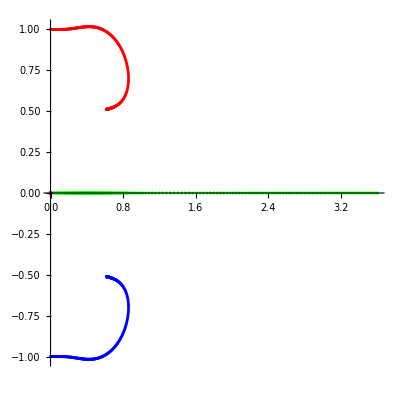

```mathematica
initpredictor//Values//N
ThetaSols[[1]]//Values//N

ComplexListPlot[{initpredictor//Values,ThetaSols[[All,1]]//Values,ThetaSols[[All,2]]//Values,ThetaSols[[All,3]]//Values,ThetaSols[[All,4]]//Values},PlotRange->All,PlotStyle->{Orange,Red,Green,Blue,Magenta},AspectRatio->1]
```

#### String configuration {4,2} where the 4-string is maximal for YD={6,6}

```mathematica
rigged={{lboxes={1,1,1,1,1,1,1,1,1,1,1,1}},{{4,2},{}},{{0,1},{0},{}}};
%//showRC
SolutionFromModeConfiguration[modes=(rigged//RiggedToModes),L=lboxes//Length];
```

-Graphics- | ∅

```mathematica
thetarels42={((x[1,1]-Λ+I/2)/(x[1,1]-Λ-I/2))((x[1,1]+I/2)/(x[1,1]-I/2))^11-(x[1,1]-x[1,2]+I)/(x[1,1]-x[1,2]-I)(x[1,1]-x[1,3]+I)/(x[1,1]-x[1,3]-I)(x[1,1]-x[1,4]+I)/(x[1,1]-x[1,4]-I)(x[1,1]-x[1,5]+I)/(x[1,1]-x[1,5]-I)(x[1,1]-x[1,6]+I)/(x[1,1]-x[1,6]-I),((x[1,2]-Λ+I/2)/(x[1,2]-Λ-I/2))((x[1,2]+I/2)/(x[1,2]-I/2))^11-(x[1,2]-x[1,1]+I)/(x[1,2]-x[1,1]-I)(x[1,2]-x[1,3]+I)/(x[1,2]-x[1,3]-I)(x[1,2]-x[1,4]+I)/(x[1,2]-x[1,4]-I)(x[1,2]-x[1,5]+I)/(x[1,2]-x[1,5]-I)(x[1,2]-x[1,6]+I)/(x[1,2]-x[1,6]-I),((x[1,3]-Λ+I/2)/(x[1,3]-Λ-I/2))((x[1,3]+I/2)/(x[1,3]-I/2))^11-(x[1,3]-x[1,1]+I)/(x[1,3]-x[1,1]-I)(x[1,3]-x[1,2]+I)/(x[1,3]-x[1,2]-I)(x[1,3]-x[1,4]+I)/(x[1,3]-x[1,4]-I)(x[1,3]-x[1,5]+I)/(x[1,3]-x[1,5]-I)(x[1,3]-x[1,6]+I)/(x[1,3]-x[1,6]-I),((x[1,4]-Λ+I/2)/(x[1,4]-Λ-I/2))((x[1,4]+I/2)/(x[1,4]-I/2))^11-(x[1,4]-x[1,1]+I)/(x[1,4]-x[1,1]-I)(x[1,4]-x[1,2]+I)/(x[1,4]-x[1,2]-I)(x[1,4]-x[1,3]+I)/(x[1,4]-x[1,3]-I)(x[1,4]-x[1,5]+I)/(x[1,4]-x[1,5]-I)(x[1,4]-x[1,6]+I)/(x[1,4]-x[1,6]-I),((x[1,6]-Λ+I/2)/(x[1,6]-Λ-I/2))((x[1,6]+I/2)/(x[1,6]-I/2))^11((x[1,5]-Λ+I/2)/(x[1,5]-Λ-I/2))((x[1,5]+I/2)/(x[1,5]-I/2))^11-(x[1,5]-x[1,1]+I)/(x[1,5]-x[1,1]-I)(x[1,5]-x[1,2]+I)/(x[1,5]-x[1,2]-I)(x[1,5]-x[1,3]+I)/(x[1,5]-x[1,3]-I)(x[1,5]-x[1,4]+I)/(x[1,5]-x[1,4]-I)(x[1,6]-x[1,1]+I)/(x[1,6]-x[1,1]-I)(x[1,6]-x[1,2]+I)/(x[1,6]-x[1,2]-I)(x[1,6]-x[1,3]+I)/(x[1,6]-x[1,3]-I)(x[1,6]-x[1,4]+I)/(x[1,6]-x[1,4]-I)}/.x[1,5]->v[2]-I/2/.x[1,6]->v[2]+I/2;
```

```mathematica
numthetarels42={(ⅈ/2+x[1,1])^11 (ⅈ/2-Λ+x[1,1])((-ⅈ/2-v[2]+x[1,1]) (-(3 ⅈ)/2-v[2]+x[1,1]) (-ⅈ+x[1,1]-x[1,2]) (-ⅈ+x[1,1]-x[1,3]) (-ⅈ+x[1,1]-x[1,4]))-Exp[I t1]((ⅈ/2-v[2]+x[1,1]) ((3 ⅈ)/2-v[2]+x[1,1]) (ⅈ+x[1,1]-x[1,2]) (ⅈ+x[1,1]-x[1,3]) (ⅈ+x[1,1]-x[1,4]))(-ⅈ/2+x[1,1])^11 (-ⅈ/2-Λ+x[1,1])+ϵ,(ⅈ/2+x[1,2])^11 (ⅈ/2-Λ+x[1,2])((-ⅈ/2-v[2]+x[1,2]) (-(3 ⅈ)/2-v[2]+x[1,2]) (-ⅈ-x[1,1]+x[1,2]) (-ⅈ+x[1,2]-x[1,3]) (-ⅈ+x[1,2]-x[1,4]))-Exp[I t1]((ⅈ/2-v[2]+x[1,2]) ((3 ⅈ)/2-v[2]+x[1,2]) (ⅈ-x[1,1]+x[1,2]) (ⅈ+x[1,2]-x[1,3]) (ⅈ+x[1,2]-x[1,4]))(-ⅈ/2+x[1,2])^11 (-ⅈ/2-Λ+x[1,2])+ϵ,(ⅈ/2+x[1,3])^11 (ⅈ/2-Λ+x[1,3])((-ⅈ/2-v[2]+x[1,3]) (-(3 ⅈ)/2-v[2]+x[1,3]) (-ⅈ-x[1,1]+x[1,3]) (-ⅈ-x[1,2]+x[1,3]) (-ⅈ+x[1,3]-x[1,4]))-Exp[I t1]((ⅈ/2-v[2]+x[1,3]) ((3 ⅈ)/2-v[2]+x[1,3]) (ⅈ-x[1,1]+x[1,3]) (ⅈ-x[1,2]+x[1,3]) (ⅈ+x[1,3]-x[1,4]))(-ⅈ/2+x[1,3])^11 (-ⅈ/2-Λ+x[1,3])+ϵ,(ⅈ/2+x[1,4])^11 (ⅈ/2-Λ+x[1,4])((-ⅈ/2-v[2]+x[1,4]) (-(3 ⅈ)/2-v[2]+x[1,4]) (-ⅈ-x[1,1]+x[1,4]) (-ⅈ-x[1,2]+x[1,4]) (-ⅈ-x[1,3]+x[1,4]))-Exp[I t1]((ⅈ/2-v[2]+x[1,4]) ((3 ⅈ)/2-v[2]+x[1,4]) (ⅈ-x[1,1]+x[1,4]) (ⅈ-x[1,2]+x[1,4]) (ⅈ-x[1,3]+x[1,4]))(-ⅈ/2+x[1,4])^11 (-ⅈ/2-Λ+x[1,4])+ϵ,((ⅈ+v[2])^11 (ⅈ-Λ+v[2]))/((-ⅈ+v[2])^11 (-ⅈ-Λ+v[2]))-Exp[0]((ⅈ/2+v[2]-x[1,1]) ((3 ⅈ)/2+v[2]-x[1,1]) (ⅈ/2+v[2]-x[1,2]) ((3 ⅈ)/2+v[2]-x[1,2]) (ⅈ/2+v[2]-x[1,3]) ((3 ⅈ)/2+v[2]-x[1,3]) (ⅈ/2+v[2]-x[1,4]) ((3 ⅈ)/2+v[2]-x[1,4]))/((-ⅈ/2+v[2]-x[1,1]) (-(3 ⅈ)/2+v[2]-x[1,1]) (-ⅈ/2+v[2]-x[1,2]) (-(3 ⅈ)/2+v[2]-x[1,2]) (-ⅈ/2+v[2]-x[1,3]) (-(3 ⅈ)/2+v[2]-x[1,3]) (-ⅈ/2+v[2]-x[1,4]) (-(3 ⅈ)/2+v[2]-x[1,4]))};
```

```mathematica
countingfunc42={Log[((x[1,1]-Λ+I/2)/(x[1,1]-Λ-I/2))]+11Log[((x[1,1]+I/2)/(x[1,1]-I/2))]-Log[(x[1,1]-x[1,2]+I)/(x[1,1]-x[1,2]-I)(x[1,1]-x[1,3]+I)/(x[1,1]-x[1,3]-I)(x[1,1]-x[1,4]+I)/(x[1,1]-x[1,4]-I)(x[1,1]-x[1,5]+I)/(x[1,1]-x[1,5]-I)(x[1,1]-x[1,6]+I)/(x[1,1]-x[1,6]-I)],Log[((x[1,2]-Λ+I/2)/(x[1,2]-Λ-I/2))]+11Log[((x[1,2]+I/2)/(x[1,2]-I/2))]-Log[(x[1,2]-x[1,1]+I)/(x[1,2]-x[1,1]-I)(x[1,2]-x[1,3]+I)/(x[1,2]-x[1,3]-I)(x[1,2]-x[1,4]+I)/(x[1,2]-x[1,4]-I)(x[1,2]-x[1,5]+I)/(x[1,2]-x[1,5]-I)(x[1,2]-x[1,6]+I)/(x[1,2]-x[1,6]-I)],Log[((x[1,3]-Λ+I/2)/(x[1,3]-Λ-I/2))]+11Log[((x[1,3]+I/2)/(x[1,3]-I/2))]-Log[(x[1,3]-x[1,1]+I)/(x[1,3]-x[1,1]-I)(x[1,3]-x[1,2]+I)/(x[1,3]-x[1,2]-I)(x[1,3]-x[1,4]+I)/(x[1,3]-x[1,4]-I)(x[1,3]-x[1,5]+I)/(x[1,3]-x[1,5]-I)(x[1,3]-x[1,6]+I)/(x[1,3]-x[1,6]-I)],Log[((x[1,4]-Λ+I/2)/(x[1,4]-Λ-I/2))]+11Log[((x[1,4]+I/2)/(x[1,4]-I/2))]-Log[(x[1,4]-x[1,1]+I)/(x[1,4]-x[1,1]-I)(x[1,4]-x[1,2]+I)/(x[1,4]-x[1,2]-I)(x[1,4]-x[1,3]+I)/(x[1,4]-x[1,3]-I)(x[1,4]-x[1,5]+I)/(x[1,4]-x[1,5]-I)(x[1,4]-x[1,6]+I)/(x[1,4]-x[1,6]-I)],Log[((x[1,6]-Λ+I/2)/(x[1,6]-Λ-I/2))((x[1,5]-Λ+I/2)/(x[1,5]-Λ-I/2))]+11Log[((x[1,6]+I/2)/(x[1,6]-I/2))((x[1,5]+I/2)/(x[1,5]-I/2))]-Log[(x[1,5]-x[1,1]+I)/(x[1,5]-x[1,1]-I)(x[1,5]-x[1,2]+I)/(x[1,5]-x[1,2]-I)(x[1,5]-x[1,3]+I)/(x[1,5]-x[1,3]-I)(x[1,5]-x[1,4]+I)/(x[1,5]-x[1,4]-I)(x[1,6]-x[1,1]+I)/(x[1,6]-x[1,1]-I)(x[1,6]-x[1,2]+I)/(x[1,6]-x[1,2]-I)(x[1,6]-x[1,3]+I)/(x[1,6]-x[1,3]-I)(x[1,6]-x[1,4]+I)/(x[1,6]-x[1,4]-I)]}/(2Pi I);
modenrs=countingfunc42/.x[1,5]->v[2]-I/2/.x[1,6]->v[2]+I/2/.Λ->0/.ϵ->0/.initpredictor//Re//Round[#,10^-1]&;
logthetarels42=(countingfunc42/.x[1,5]->v[2]-I/2/.x[1,6]->v[2]+I/2)-modenrs;
```

```mathematica
Thetavars={x[1,1],x[1,2],x[1,3],x[1,4],v[2]};
δ=-10^-10;
initpredictor={x[1,1]->v[1,4,1]+1.5I-δ,x[1,2]->v[1,4,1]+0.5I+δ,x[1,3]->v[1,4,1]-0.5I-δ,x[1,4]->v[1,4,1]-1.5I+δ,v[2]->v[1,2,1]}/.(v[1,x_,y_]:>-v[1,x,y])/.sol[1]
initpredictor=FindRoot[numthetarels42/.ϵ->0/.t1->0/.Λ->0,{Thetavars,Thetavars/.(initpredictor)}//Transpose,WorkingPrecision->20,MaxIterations->1000]
```

{x[1,1]→0.228616+1.5 ⅈ,x[1,2]→0.228616+0.5 ⅈ,x[1,3]→0.228616-0.5 ⅈ,x[1,4]→0.228616-1.5 ⅈ,v[2]→-0.3943351818869249518733547879537048400268}

{x[1,1]→0.18949459537249622691+1.5332596606692196651 ⅈ,x[1,2]→0.20743019961108203163+0.500000000929313543 ⅈ,x[1,3]→0.20743019961108203163-0.50000000092931286638 ⅈ,x[1,4]→0.18949459537249631577-1.5332596606692186714 ⅈ,v[2]→-0.39695507417281093843-6.8695209458733923574×10^-17 ⅈ}

```mathematica
dϵ=10^-2;
predictor=initpredictor;
(*predictor=ThetaSols[[-1]];*)
Sols={};
Do[
minsolrep=FindRoot[numthetarels42/.ϵ->dϵ-i dϵ/10/.t1->0/.Λ->0,{Thetavars,Thetavars/.predictor}//Transpose,WorkingPrecision->60,MaxIterations->1000];AppendTo[Sols,minsolrep];predictor=minsolrep;,{i,0,100}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than 60. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

$Aborted

```mathematica
predictor=initpredictor;
(*predictor=Sols[[-1]];*)
Sols={};
Do[
minsolrep=FindRoot[numthetarels42/.ϵ->0/.t1->i 1/10/.Λ->0,{Thetavars,Thetavars/.predictor}//Transpose];AppendTo[Sols,minsolrep];predictor=minsolrep;,{i,0,10}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
ThetaSols={};
Thetas={};
predictor=initpredictor;
Do[
minsolrep=FindRoot[numthetarels42/.ϵ->0/.t1->0/.Λ->i,{Thetavars,Thetavars/.predictor}//Transpose,WorkingPrecision->100,MaxIterations->1000];AppendTo[ThetaSols,minsolrep];AppendTo[Thetas,i];predictor=minsolrep;,{i,0,5,1/20}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{-0.189495+1.53326 ⅈ,-0.20743+0.5 ⅈ,-0.20743-0.5 ⅈ,-0.189495-1.53326 ⅈ,0.396955-1.50353×10^-16 ⅈ}

{-0.189495+1.53326 ⅈ,-0.20743+0.5 ⅈ,-0.20743-0.5 ⅈ,-0.189495-1.53326 ⅈ,0.396955-3.97762×10^-109 ⅈ}

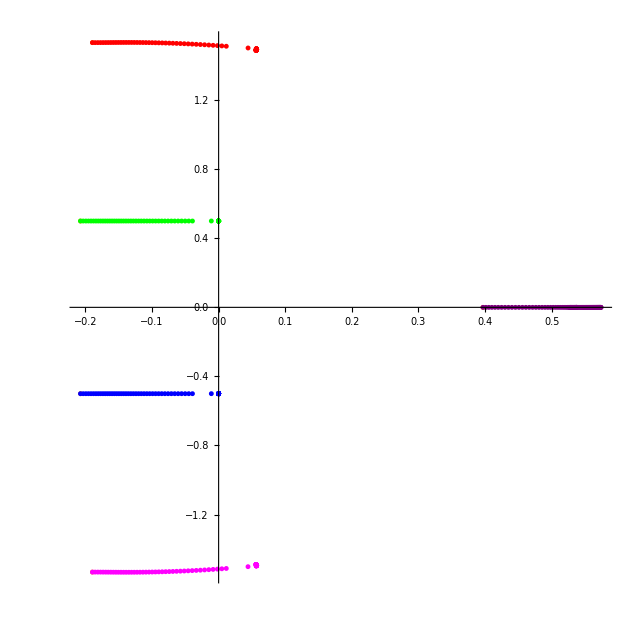

```mathematica
initpredictor//Values//N
ThetaSols[[1]]//Values//N

ComplexListPlot[{initpredictor//Values,ThetaSols[[All,1]]//Values,ThetaSols[[All,2]]//Values,ThetaSols[[All,3]]//Values,ThetaSols[[All,4]]//Values,ThetaSols[[All,5]]//Values},PlotRange->All,PlotStyle->{Orange,Red,Green,Blue,Magenta,Purple},AspectRatio->1]
```

```mathematica
LUDecomposition[D[numthetarels42,{Thetavars}]/.t1->0/.Λ->0/.initpredictor][[3]]
```

LUDecomposition::luc: Result for LUDecomposition of badly conditioned matrix {{-6499.676708+504.274484 ⅈ,7708.244866+35.477093 ⅈ,167.1761912+88.03788327 ⅈ,61.57875005+34.28176796 ⅈ,-262.3312112+505.643518 ⅈ},«3»,{1.782724253-0.7225931231 ⅈ,«3»,5.920029787+«60» ⅈ}} may contain significant numerical errors.

2.036621593×10^12

### Mode numbers for exact strings

```mathematica
(*Function that takes a set of roots {x[1,0,1]->a1,x[1,0,2]->a2,...,x[N,0,p]->aq} and produces a nested list where the first nested level corresponds to the nesting of the BAE and the second corresponds to strings within this nested level*)

(*There is no algorithm to check if there are several ways to make strings that look more or less equally good. This must be done by hand.*)

StringSorter[rootsExact_]:=(
dδ=0.3;
allLevelstrings={};
Do[rootvals=rootsExact/.(x[a_,0,b_]->n_):>If[a==i,x[a,0,b]->n,Nothing]//Values;
strings={};
While[Length[rootvals]>0,string={Extract[rootvals,PositionLargest[rootvals//Im][[1]]]};
stringlength=Min[2(string[[1]]//Im//Round[#,0.1]&)+1//Round,Length[rootvals]];

Do[
step0=string[[-1]];
step1=(step0//Im)-1;
step2=Select[rootvals,step1-dδ<(#//Im)<step1+dδ&];
step3=PositionSmallest[Abs[#-step0//Re]&/@step2][[1]];
step4=Extract[step2,step3];
AppendTo[string,step4];,Ceiling[stringlength/2]-1];
Do[step5=Extract[rootvals,PositionSmallest[Abs[#-(string[[i]]//Conjugate)]&/@rootvals]];AppendTo[string,step5],{i,Floor[stringlength/2]}];

AppendTo[strings,string//SortBy[#,(#//Im&),Greater]&];
rootvals=DeleteElements[rootvals,string];
];
AppendTo[allLevelstrings,strings]
,{i,(rootsExact//Keys)[[All,1]]//Max}
];
allLevelstrings=Flatten[SortBy[#,(#[[1]]//Re)&]&/@GatherBy[#,(#//Length)&],1]&/@allLevelstrings;
Table[k=0;Table[k++;x[a,0,k]->allLevelstrings[[a,b,c]],{b,Length[allLevelstrings[[a]]]},{c,Length[allLevelstrings[[a,b]]]}],{a,Length[allLevelstrings]}])

(*Problems: 1. If highest values deviates much from multiple of I/2 or I, the guess for stringlength can be wrong*)
```

```mathematica
MatchingFunction[stringset1_,stringset2_,m_]:=(
weightNum[weightlist_]:=ReplaceAt[#,n_:>n+m I,2]&/@weightlist;
weightDenom[weightlist_]:=ReplaceAt[#,n_:>n-m I,2]&/@weightlist;
weightDenomReverse[weightlist_]:=ReplaceAt[#,n_:>-(n-m I),2]&/@weightlist;

weightgroup1=Table[((Length[stringset1]+1)/2-k)I,{k,1,Length[stringset1]}];
weightgroup2=Table[((Length[stringset2]+1)/2-k)I,{k,1,Length[stringset2]}];
weightlist=(Table[{stringset1[[i]]-stringset2[[j]],weightgroup1[[i]]-weightgroup2[[j]]},{i,Length[stringset1]},{j,Length[stringset2]}]//Flatten[#,1]&)/.{0,0}->Nothing;

Matches={};
cancellations=0;
weightlistNum=weightNum[weightlist];
weightlistDenom=weightDenom[weightlist];
Do[
test=Select[weightlistDenom,#[[2]]==numC[[2]]&&!MemberQ[Matches[[All,2]],#[[1]]]&];
If[Length[test]>0,AppendTo[Matches,{numC[[1]],test[[1,1]]}];cancellations++];,{numC,weightlistNum}];

weightlistNum=Select[weightNum[weightlist],!MemberQ[Matches[[All,1]],#[[1]]]&];
weightlistDenom=Select[weightDenomReverse[weightlist],!MemberQ[Matches[[All,2]],#[[1]]]&];

If[Length[(taken=Select[weightlistDenom,MemberQ[weightlistNum,#]&])]>0,Matches=Join[Matches,{#,#}&/@(taken[[All,1]])]];
weightlistNum=DeleteElements[weightlistNum,taken];
weightlistDenom=DeleteElements[weightlistDenom,taken];

Do[consid=weightlistNum[[i]];
match=Select[weightlistDenom,#[[2]]==consid[[2]]&][[1]];
weightlistDenom=DeleteElements[weightlistDenom,match];
AppendTo[Matches,{consid[[1]],match[[1]]}];,{i,Length[weightlistNum]}];)

MatchingFunction[stringset1_,stringset2_,m_]:=(
weightNum[weightlist_]:=ReplaceAt[#,n_:>n+m I,2]&/@weightlist;
weightDenom[weightlist_]:=ReplaceAt[#,n_:>n-m I,2]&/@weightlist;
weightDenomReverse[weightlist_]:=ReplaceAt[#,n_:>-(n-m I),2]&/@weightlist;

weightgroup1=Table[((Length[stringset1]+1)/2-k)I,{k,1,Length[stringset1]}];
weightgroup2=Table[((Length[stringset2]+1)/2-k)I,{k,1,Length[stringset2]}];
weightlist=(Table[{stringset1[[i]]-stringset2[[j]],weightgroup1[[i]]-weightgroup2[[j]]},{i,Length[stringset1]},{j,Length[stringset2]}]//Flatten[#,1]&)/.{0,0}->Nothing;

CancellationMatches={};
weightlistNum=weightNum[weightlist];
weightlistDenom=weightDenom[weightlist];
Do[
test=Select[weightlistDenom,#[[2]]==numC[[2]]&&!MemberQ[CancellationMatches[[All,2]],#[[1]]]&];
If[Length[test]>0,AppendTo[CancellationMatches,{numC[[1]],test[[1,1]]}]];,{numC,weightlistNum}];

weightlistNum=Select[weightNum[weightlist],!MemberQ[CancellationMatches[[All,1]],#[[1]]]&];
weightlistDenom=Select[weightDenomReverse[weightlist],!MemberQ[CancellationMatches[[All,2]],#[[1]]]&];

Matches={};
If[Length[(taken=Select[weightlistDenom,MemberQ[weightlistNum,#]&])]>0,Matches=Join[Matches,{#,#}&/@(taken[[All,1]])]];
weightlistNum=DeleteElements[weightlistNum,taken];
weightlistDenom=DeleteElements[weightlistDenom,taken];

Do[consid=weightlistNum[[i]];
match=Select[weightlistDenom,#[[2]]==consid[[2]]&][[1]];
weightlistDenom=DeleteElements[weightlistDenom,match];
AppendTo[Matches,{consid[[1]],match[[1]]}];,{i,Length[weightlistNum]}];)
```

```mathematica
numrel22={((ⅈ/2+x[1,1]) (ⅈ/2+x[1,2]))^ll(-ⅈ+x[1,1]-x[1,3]) (ⅈ-x[1,2]+x[1,3]) (-ⅈ+x[1,1]-x[1,4]) (-ⅈ+x[1,2]-x[1,4])-((-ⅈ/2+x[1,1]) (-ⅈ/2+x[1,2]))^ll(ⅈ+x[1,1]-x[1,3]) (ⅈ+x[1,2]-x[1,3]) (ⅈ+x[1,1]-x[1,4]) (ⅈ+x[1,2]-x[1,4]),((ⅈ/2+x[1,3]) (ⅈ/2+x[1,4]))^ll(ⅈ+x[1,1]-x[1,3]) (-ⅈ-x[1,2]+x[1,3]) (ⅈ+x[1,1]-x[1,4]) (ⅈ+x[1,2]-x[1,4])-((-ⅈ/2+x[1,3]) (-ⅈ/2+x[1,4]))^ll(-ⅈ+x[1,1]-x[1,3]) (ⅈ-x[1,2]+x[1,3]) (-ⅈ+x[1,1]-x[1,4]) (-ⅈ+x[1,2]-x[1,4])};
varsX={x[1,1],x[1,2],x[1,3],x[1,4]};
```

```mathematica
eq11=(x[1,1]+I/2)^ll(x[1,1]-x[1,2]-I)(x[1,1]-x[1,3]-I)(x[1,1]-x[1,4]-I)-(x[1,1]-I/2)^ll(x[1,1]-x[1,2]+I)(x[1,1]-x[1,3]+I)(x[1,1]-x[1,4]+I);eq12=eq11/.{x[1,1]->x[1,2],x[1,2]->x[1,1]};
eq13=eq11/.{x[1,1]->x[1,3],x[1,3]->x[1,1]};
eq14=eq11/.{x[1,1]->x[1,4],x[1,4]->x[1,1]};
```

```mathematica
numrel22=Join[{eq11},{eq12},{eq13},{eq14}]
```

{(ⅈ/2+x[1,1])^ll (-ⅈ+x[1,1]-x[1,2]) (-ⅈ+x[1,1]-x[1,3]) (-ⅈ+x[1,1]-x[1,4])-(-ⅈ/2+x[1,1])^ll (ⅈ+x[1,1]-x[1,2]) (ⅈ+x[1,1]-x[1,3]) (ⅈ+x[1,1]-x[1,4]),(ⅈ/2+x[1,2])^ll (-ⅈ-x[1,1]+x[1,2]) (-ⅈ+x[1,2]-x[1,3]) (-ⅈ+x[1,2]-x[1,4])-(-ⅈ/2+x[1,2])^ll (ⅈ-x[1,1]+x[1,2]) (ⅈ+x[1,2]-x[1,3]) (ⅈ+x[1,2]-x[1,4]),(ⅈ/2+x[1,3])^ll (-ⅈ-x[1,1]+x[1,3]) (-ⅈ-x[1,2]+x[1,3]) (-ⅈ+x[1,3]-x[1,4])-(-ⅈ/2+x[1,3])^ll (ⅈ-x[1,1]+x[1,3]) (ⅈ-x[1,2]+x[1,3]) (ⅈ+x[1,3]-x[1,4]),(ⅈ/2+x[1,4])^ll (-ⅈ-x[1,1]+x[1,4]) (-ⅈ-x[1,2]+x[1,4]) (-ⅈ-x[1,3]+x[1,4])-(-ⅈ/2+x[1,4])^ll (ⅈ-x[1,1]+x[1,4]) (ⅈ-x[1,2]+x[1,4]) (ⅈ-x[1,3]+x[1,4])}

```mathematica
varsX
```

{x[1,1],x[1,2],x[1,3],x[1,4]}

```mathematica
numrel22/.ll->8/.(rootsExact/.x[a_,b_,c_]:>x[a,c])
```

{5.328338260483097839044×10^-17+2.087145857753475427513×10^-17 ⅈ,-5.328338260483097839044×10^-17+2.087145857753475427513×10^-17 ⅈ,-5.328338260483097839044×10^-17+2.087145857753475427513×10^-17 ⅈ,5.328338260483097839044×10^-17+2.087145857753475427513×10^-17 ⅈ}

```mathematica
ThetaSols={};
Thetas={};
predictor=rootsExact/.x[a_,b_,c_]:>x[a,c];
Do[
minsolrep=FindRoot[numrel22/.ll->i,{varsX,varsX/.predictor}//Transpose,WorkingPrecision->20,MaxIterations->1000];AppendTo[ThetaSols,minsolrep];AppendTo[Thetas,i];predictor=minsolrep;,{i,8,100,1/10}]
```

```mathematica
rootsExact/.x[a_,b_,c_]:>x[a,c]
ThetaSols[[-1]]
```

{x[1,1]→-0.463264727589030903416266285302077177767-0.502293853569902609393034628730605337166 ⅈ,x[1,2]→-0.463264727589030903416266285302077177767+0.502293853569902609393034628730605337166 ⅈ,x[1,3]→0.463264727589030903416266285302077177767-0.502293853569902609393034628730605337166 ⅈ,x[1,4]→0.463264727589030903416266285302077177767+0.502293853569902609393034628730605337166 ⅈ}

{x[1,1]→-15.427137212501845884-1.5866911145287830824 ⅈ,x[1,2]→-15.427137212501845884+1.5866911145287830824 ⅈ,x[1,3]→15.427137212501845884-1.5866911145287830824 ⅈ,x[1,4]→15.427137212501845884+1.5866911145287830824 ⅈ}

```mathematica
apprstring=Thread[varsS->{0.4632647275890309034162662853020771777671793839623699683243`39.46377209956328,-0.4632647275890309034162662853020771777671793839623699683244`39.46377209956328}]
```

{v[1,2,1]→0.463264727589030903416266285302077177767,v[1,2,2]→-0.463264727589030903416266285302077177767}

```mathematica
Allrels
```

```mathematica
stringll={-1/2+(ll ArcTan[v[1,2,1]])/π-(ArcTan[1/2 (v[1,2,1]-v[1,2,2])]/π+(2 ArcTan[v[1,2,1]-v[1,2,2]])/π),1/2+(ll ArcTan[v[1,2,2]])/π-(-(2 ArcTan[v[1,2,1]-v[1,2,2]])/π+ArcTan[1/2 (-v[1,2,1]+v[1,2,2])]/π)};
varsS=sol[1]//Keys;
```

```mathematica
ThetaSols={};
Thetas={};
predictor=sol[1];
Do[
minsolrep=FindRoot[stringll/.ll->i,{varsS,varsS/.predictor}//Transpose,WorkingPrecision->20,MaxIterations->1000];AppendTo[ThetaSols,minsolrep];AppendTo[Thetas,i];predictor=minsolrep;,{i,8,100,1/10}]
```

```mathematica
sol[1]
ThetaSols[[-1]]
```

{v[1,2,1]→0.4711719514470233524110542308503534391972,v[1,2,2]→-0.4711719514470233524110542308503534391972}

{v[1,2,1]→0.016536014903737135999,v[1,2,2]→-0.016536014903737135999}

```mathematica
(*Creates fused BAE and counting functions*)

FusingBAE[stringconfig_,yd_]:=(
Q[x_,n_]:=If[x===0&&n===0,1,(x+n I)/(x-n I)];

Qppnn[a_,i_]:=Product[Q[x[a,i]-x[a,j],1],{j,1,MM[a,0,yd]}];
Apn[a_,i_]:=Product[Q[x[a,i]-x[a-1,j],1/2],{j,1,MM[a-1,0,yd]}]/.x[0,n_]:>θ[n]/.θ[n_]:>0;
Bpn[a_,i_]:=Product[Q[x[a,i]-x[a+1,j],1/2],{j,1,MM[a+1,0,yd]}];

vargroups={};
Allrelfused=Table[stringgroups=TakeList[Range[MM[a,0,yd]],stringconfig[[a]]];AppendTo[vargroups,Table[x[a,i],{j,Length[stringgroups]},{i,stringgroups[[j]]}]];
fusedQ=log[Table[Product[-Qppnn[a,i],{i,stringgroups[[j]]}]//Cancel,{j,Length[stringgroups]}],0,branch];
fusedA=If[a==1,Total[yd]log[Table[Product[Q[x[a,i],1/2],{i,stringgroups[[j]]}],{j,Length[stringgroups]}],0,branch],log[Table[Product[Apn[a,i],{i,stringgroups[[j]]}],{j,Length[stringgroups]}],0,branch]];
fusedB=log[Table[Product[Bpn[a,i],{i,stringgroups[[j]]}],{j,Length[stringgroups]}],0,branch];
fusedA+fusedB-fusedQ/.branch->branchchoice,{a,1,Length[yd]-1}];
orgvargroups=GatherBy[#,Length]&/@vargroups;)

CountingFunctionString[stringconfig_,length_]:=(
vargroups=Table[Map[x[a,#]&,TakeList[Range[Total[stringconfig[[a]]]],stringconfig[[a]]],{2}],{a,Length[stringconfig]-1}];

Table[
cancelsQ=0;
AllMatchesQ=Table[If[ss==s,Nothing,MatchingFunction[vargroups[[a,s]],vargroups[[a,ss]],1];cancelsQ+=cancellations;Matches],{ss,1,Length[vargroups[[a]]]}]//Flatten[#,1]&;

cancelsA=0;
AllMatchesA=If[a==1,MatchingFunction[vargroups[[a,s]],{0},1/2];cancelsA+=cancellations;Matches,Table[MatchingFunction[vargroups[[a,s]],vargroups[[a-1,ss]],1/2];cancelsA+=cancellations;Matches,{ss,1,Length[vargroups[[a-1]]]}]//Flatten[#,1]&];

cancelsB=0;
AllMatchesB=If[a==Length[vargroups],{},Table[MatchingFunction[vargroups[[a,s]],vargroups[[a+1,ss]],1/2];cancelsB+=cancellations;Matches,{ss,1,Length[vargroups[[a+1]]]}]]//Flatten[#,1]&;

logQ=log[(#[[1]]+I)/(#[[2]]-I),-1,branch]/(-2Pi I)-1/2&/@AllMatchesQ;
logA=If[a==1,length  (log[(#[[1]]+I/2)/(#[[2]]-I/2),-1,branch]/(-2Pi I)-1/2)&/@AllMatchesA(*;{length log[Times@@((#[[1]]+I/2)/(#[[2]]-I/2)&/@AllMatchesA),-1,branch]/(-2Pi I)-1/2}*), log[(#[[1]]+I/2)/(#[[2]]-I/2),-1,branch]/(-2Pi I)-1/2&/@AllMatchesA];
logB=log[(#[[1]]+I/2)/(#[[2]]-I/2),-1,branch]/(-2Pi I)-1/2&/@AllMatchesB;
-(Total[logA]+If[a==1,length,1]cancelsA/2+Total[logB]+cancelsB/2-Total[logQ]-cancelsQ/2)/.branch->branchchoice
,{a,Length[vargroups]},{s,Length[vargroups[[a]]]}]
)

CountingFunctionString[stringconfig_,length_]:=(
vargroups=Table[Map[x[a,#]&,TakeList[Range[Total[stringconfig[[a]]]],stringconfig[[a]]],{2}],{a,Length[stringconfig]-1}];

Table[

AllMatchesQ=Table[If[ss==s,Nothing,MatchingFunction[vargroups[[a,s]],vargroups[[a,ss]],1];Cancelfactors=(#[[1]]+I)/(#[[2]]-I)&/@CancellationMatches;Truefactors=(#[[1]]+I)/(#[[2]]-I)&/@Matches;Truefactors[[1]]=Truefactors[[1]] (Times@@Cancelfactors);Truefactors],{ss,1,Length[vargroups[[a]]]}]//Flatten[#,1]&;

AllMatchesA=If[a==1,MatchingFunction[vargroups[[a,s]],{0},1/2];Cancelfactors=(#[[1]]+I/2)/(#[[2]]-I/2)&/@CancellationMatches;Truefactors=(#[[1]]+I/2)/(#[[2]]-I/2)&/@Matches;Truefactors[[1]]=Truefactors[[1]] (Times@@Cancelfactors);Truefactors,Table[MatchingFunction[vargroups[[a,s]],vargroups[[a-1,ss]],1/2];Cancelfactors=(#[[1]]+I/2)/(#[[2]]-I/2)&/@CancellationMatches;Truefactors=(#[[1]]+I/2)/(#[[2]]-I/2)&/@Matches;Truefactors[[1]]=Truefactors[[1]] (Times@@Cancelfactors);Truefactors,{ss,1,Length[vargroups[[a-1]]]}]//Flatten[#,1]&];

AllMatchesB=If[a==Length[vargroups],{},Table[MatchingFunction[vargroups[[a,s]],vargroups[[a+1,ss]],1/2];Cancelfactors=(#[[1]]+I/2)/(#[[2]]-I/2)&/@CancellationMatches;Truefactors=(#[[1]]+I/2)/(#[[2]]-I/2)&/@Matches;Truefactors[[1]]=Truefactors[[1]] (Times@@Cancelfactors);Truefactors,{ss,1,Length[vargroups[[a+1]]]}]]//Flatten[#,1]&;

logQ=log[#,-1,branch]/(-2Pi I)-1/2&/@AllMatchesQ;
logA=If[a==1,length  (log[#,-1,branch]/(-2Pi I)-1/2)&/@AllMatchesA(*;{length log[Times@@((#[[1]]+I/2)/(#[[2]]-I/2)&/@AllMatchesA),-1,branch]/(-2Pi I)-1/2}*), log[#,-1,branch]/(-2Pi I)-1/2&/@AllMatchesA];
logB=log[#,-1,branch]/(-2Pi I)-1/2&/@AllMatchesB;
-(Total[logA]+Total[logB]-Total[logQ])/.branch->branchchoice
,{a,Length[vargroups]},{s,Length[vargroups[[a]]]}]
)

CountingFunctionKS[stringconfig_,length_]:=(
vargroups=Table[Map[x[a,#]&,TakeList[Range[Total[stringconfig[[a]]]],stringconfig[[a]]],{2}],{a,Length[stringconfig]-1}];

Table[

AllMatchesQ={(#[[1]]-#[[2]]),(#[[1]]-#[[2]])}&/@(Table[If[ss==s,Nothing,Tuples[{vargroups[[a,s]],vargroups[[a,ss]]}]],{ss,1,Length[vargroups[[a]]]}]//Flatten[#,1]&);

AllMatchesA=If[a==1,{vargroups[[a,s]],vargroups[[a,s]]}//Transpose,{(#[[1]]-#[[2]]),(#[[1]]-#[[2]])}&/@(Table[Tuples[{vargroups[[a,s]],vargroups[[a-1,ss]]}],{ss,1,Length[vargroups[[a-1]]]}]//Flatten[#,1]&)];

AllMatchesB={(#[[1]]-#[[2]]),(#[[1]]-#[[2]])}&/@(If[a==Length[vargroups],{},Table[Tuples[{vargroups[[a,s]],vargroups[[a+1,ss]]}],{ss,1,Length[vargroups[[a+1]]]}]]//Flatten[#,1]&);


logQ=log[(#[[1]]+I)/(#[[2]]-I),-1,branch]/(-2Pi I)-1/2&/@AllMatchesQ;
logA=If[a==1,length  (log[(#[[1]]+I/2)/(#[[2]]-I/2),-1,branch]/(-2Pi I)-1/2)&/@AllMatchesA, log[(#[[1]]+I/2)/(#[[2]]-I/2),-1,branch]/(-2Pi I)-1/2&/@AllMatchesA];
logB=log[(#[[1]]+I/2)/(#[[2]]-I/2),-1,branch]/(-2Pi I)-1/2&/@AllMatchesB;

-(Total[logA]+Total[logB]-Total[logQ])/.branch->branchchoice,{a,Length[vargroups]},{s,Length[vargroups[[a]]]}])
```

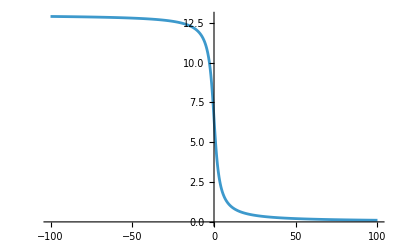

```mathematica
Plot[13 (ⅈ (π+Arg[-(((ⅈ/2+x[1,1]) (ⅈ/2+x[1,2]) (ⅈ/2+x[1,3]) (ⅈ/2+x[1,4]) (ⅈ/2+x[1,5]))/((-ⅈ/2+x[1,1]) (-ⅈ/2+x[1,2]) (-ⅈ/2+x[1,3]) (-ⅈ/2+x[1,4]) (-ⅈ/2+x[1,5])))])+Log[Abs[((ⅈ/2+x[1,1]) (ⅈ/2+x[1,2]) (ⅈ/2+x[1,3]) (ⅈ/2+x[1,4]) (ⅈ/2+x[1,5]))/((-ⅈ/2+x[1,1]) (-ⅈ/2+x[1,2]) (-ⅈ/2+x[1,3]) (-ⅈ/2+x[1,4]) (-ⅈ/2+x[1,5]))]])/(2Pi I)/.{x[1,1]->2 ⅈ+v[1,5,1],x[1,2]->ⅈ+v[1,5,1]+I ϵ,x[1,3]->v[1,5,1],x[1,4]->-ⅈ+v[1,5,1]-I ϵ,x[1,5]->-2 ⅈ+v[1,5,1],x[1,6]->v[1,1,1]}/.ϵ->0//Re,{v[1,5,1],-100,100}]
```

```mathematica
Series[(x-I/2-I ϵ)/(x-I/2+I ϵ)(x+I/2-I ϵ)/(x+I/2+I ϵ)(x+5I/2+I ϵ)/(x-5I/2-I ϵ),{ϵ,0,2}]
```

((5 ⅈ)/2+x)/(-(5 ⅈ)/2+x)-(8 ⅈ x (49+4 x^2) ϵ)/((-5 ⅈ+2 x)^2 (1+4 x^2))-(16 (x (1-960 ⅈ x+392 x^2+16 x^4)) ϵ^2)/((-5 ⅈ+2 x)^3 (1+4 x^2)^2)+O[ϵ]^3

```mathematica
Solve[((5 ⅈ)/2+x)/(-(5 ⅈ)/2+x)-(8 ⅈ x (49+4 x^2) ϵ)/((-5 ⅈ+2 x)^2 (1+4 x^2))==1,x]/.ϵ->-0.05
```

{{x→0.+0.444785 ⅈ},{x→0.-0.540866 ⅈ},{x→0.+2.54706 ⅈ}}

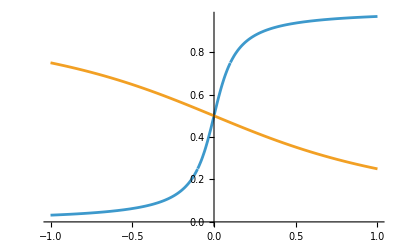

```mathematica
Plot[1/(2Pi I){log[(x-I ϵ)/(x+I ϵ),0,0],log[(x+I)/(x-I),0,0]}/.ϵ->0.1//Evaluate,{x,-1,1}]
Manipulate[Plot[{1/(2Pi I)(log[(x-I/2-I ϵ)/(x-I/2+I ϵ)(x+I/2-I ϵ)/(x+I/2+I ϵ)(x+5I/2+I ϵ)/(x-5I/2-I ϵ),0,0])}//Re//Evaluate,{x,-1,1}],{ϵ,-1,1}]
Manipulate[Plot[{1/(2Pi I)(log[(x-I ϵ)/(x+I ϵ)(x+2I+I ϵ)/(x-2I-I ϵ),0,0]),1/(2Pi I)(log[(x-I ϵ)/(x+I ϵ)(x+I)/(x-I),0,0])}//Re//Evaluate,{x,-1,1},PlotStyle->{Red,Blue}],{ϵ,-1,1}]
```

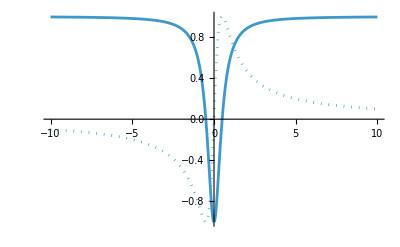

```mathematica
ReImPlot[{(x-I ϵ)/(x+I ϵ)}/.ϵ->-0.5//Evaluate,{x,-10,10},PlotRange->All]
```

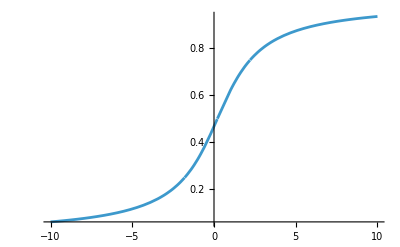

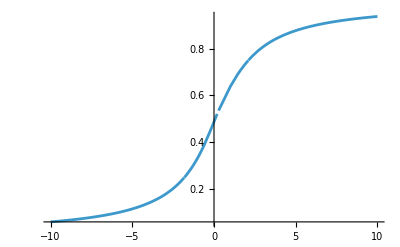

```mathematica
Plot[log[(x[1,0,2]-x[1,0,6]+I)/(x[1,0,4]-x[1,0,6]-I),0,0]/(2Pi I)/.x[1,0,6]->x/.(rootsExact//RootsInStrings//Flatten)//Re//Evaluate,{x,-10,10},PlotRange->All]
Plot[log[(x[1,0,5]-x[1,0,6]+I)/(x[1,0,3]-x[1,0,6]-I)(x[1,0,4]-x[1,0,6]+I)/(x[1,0,2]-x[1,0,6]-I)(x[1,0,3]-x[1,0,6]+I)/(x[1,0,1]-x[1,0,6]-I)(x[1,0,2]-x[1,0,6]+I)/(x[1,0,4]-x[1,0,6]-I),0,0]/(2Pi I)/.x[1,0,6]->x/.(rootsExact//RootsInStrings//Flatten)//Re//Evaluate,{x,-10,10},PlotRange->All]
```

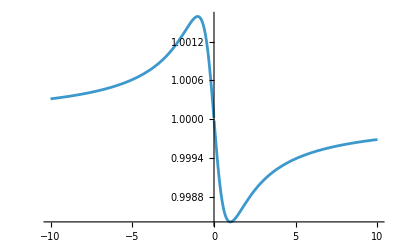

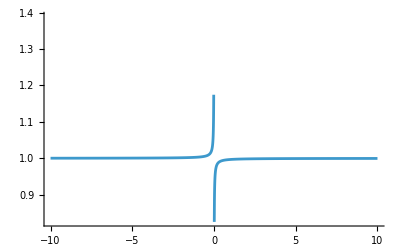

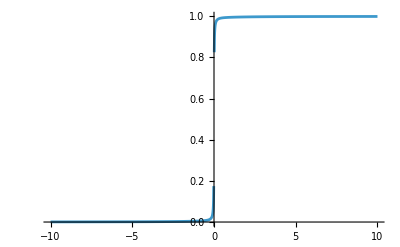

```mathematica
Plot[log[(-ⅈ ϵ-I+x)/(ⅈ ϵ-I+x),0,0]/(2Pi I)+(1-KroneckerDelta[ϵ])(-Sign[ϵ]HeavisideTheta[x]+HeavisideTheta[ϵ])/.ϵ->0.01//Re//Evaluate,{x,-10,10},PlotRange->All]
Plot[log[(-ⅈ ϵ+x)/(ⅈ ϵ+x),0,0]/(2Pi I)+(1-KroneckerDelta[ϵ])(-Sign[ϵ]HeavisideTheta[x]+HeavisideTheta[ϵ])/.ϵ->0.01//Re//Evaluate,{x,-10,10},PlotRange->All]
Plot[log[(-ⅈ ϵ+x)/(ⅈ ϵ+x)(-ⅈ ϵ-I+x)/(ⅈ ϵ-I+x),0,0]/(2Pi I)/.ϵ->0.01//Re//Evaluate,{x,-10,10},PlotRange->All]
```

```mathematica
YQa[a_,s_,YD_]:=u^MM[a,s,YD]+Sum[c[a,s,k] u^(MM[a,s,YD]-k),{k,MM[a,s,YD]}];

(*Gives roots from centres of strings symbolically*)
BetheRootsFromStrings[stringconfig_]:=
(vargroups=Table[Map[x[a,#]&,TakeList[Range[Total[stringconfig[[a]]]],stringconfig[[a]]],{2}],{a,Length[stringconfig]-1}];
orgvargroups=GatherBy[#,Length]&/@vargroups;
stringToXroots=Table[(k=Position[orgvargroups[[i,j,m]],#][[1,1]]-(Length[orgvargroups[[i,j,m]]]-1)/2-1;#/.x[a_,n_]:>(x[a,n]->v[i,Length[orgvargroups[[i,j,1]]],m]-k I))&/@orgvargroups[[i,j,m]],{i,Length[orgvargroups]},{j,Length[orgvargroups[[i]]]},{m,Length[orgvargroups[[i,j]]]}]//Flatten)

(*Gives roots from c coefficients numerically*)
rootsfromcoeff[YD_,sol_]:=Block[{k},Table[If[{a,s}!={0,0},k=1;ReplaceAll[#,u->x[a,s,k++]]&/@(NSolve[YQa[a,s,YD]/.sol,u]//Flatten),Nothing],{a,0,Length[YD]-1},{s,0,YD[[a+1]]-1}]//Flatten];
```

#### Comparing mode numbers

```mathematica
(*Finding an exact solution*)
exactsol=SolutionSYTW[SYT=RandomTableau[{6,5,4,2}]];
(*exactsol=SolutionSYTW[SYT={{{1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{4,2,1,1,1},{4,1},{1},{}},{{1,2,1,3,4},{0,1},{0},{}}}//ToSYT];*)
```

Proceeding with HomotopyContinuation for result_{{1}, {2}}.csv.

Proceeding with HomotopyContinuation for result_{{1}, {2}, {3}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4}, {2}, {3}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4}, {2}, {3}, {5}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4, 6}, {2}, {3}, {5}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4, 6}, {2, 7}, {3}, {5}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4, 6}, {2, 7}, {3, 8}, {5}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4, 6, 9}, {2, 7}, {3, 8}, {5}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4, 6, 9}, {2, 7}, {3, 8}, {5, 10}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4, 6, 9, 11}, {2, 7}, {3, 8}, {5, 10}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4, 6, 9, 11}, {2, 7, 12}, {3, 8}, {5, 10}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4, 6, 9, 11}, {2, 7, 12}, {3, 8, 13}, {5, 10}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4, 6, 9, 11}, {2, 7, 12, 14}, {3, 8, 13}, {5, 10}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4, 6, 9, 11, 15}, {2, 7, 12, 14}, {3, 8, 13}, {5, 10}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4, 6, 9, 11, 15}, {2, 7, 12, 14}, {3, 8, 13, 16}, {5, 10}}.csv.

Proceeding with HomotopyContinuation for result_{{1, 4, 6, 9, 11, 15}, {2, 7, 12, 14, 17}, {3, 8, 13, 16}, {5, 10}}.csv.

```mathematica
(*Choosing a rigged configuration to compare with*)
rigged=SYT//ToRiggedExact[#]&;
(*rigged={{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{5,1,1,1,1,1},{4,1},{1},{}},{{2,1,3,5,5,7},{0,1},{0},{}}};*)
SYTlist=Table[Select[MemberQ[Range[1,i],#]&]/@SYT/.{{}->Nothing},{i,Count[SYT[[1]]-Range[SYT[[1]]//Length],0],SYT//Max}][[2;;]];
rigged=SYTlist[[λTchoice=-1]]//ToRiggedExact[#]&;
rigged//showRC
```

-Graphics- | -Graphics- | -Graphics- | ∅

```mathematica
(*Finding a string solution*)
SolutionFromModeConfiguration[modes=(rigged//RiggedToModes),rigged[[1,1]]//Length];
```

{{0,-1.,5.,4.,2.,1.,0,-2.,-3.},{0.5,2.,1.,0,-1.},{1.,0}}

{{-10.,-12.,5.5,4.5,2.5,1.5,0.5,-1.5,-2.5},{-4.,3.,2.,1.,0},{1.5,0.5}}

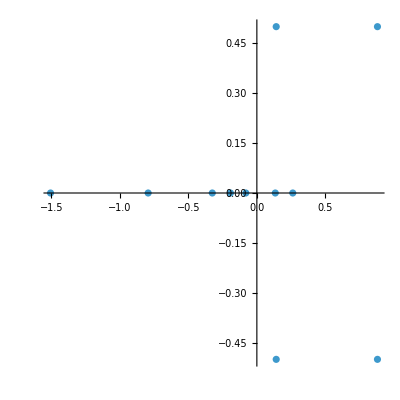

```mathematica
(*Mode numbers of the string solution*)
branchchoice=0;
CountingFunctionString[rigged[[2]],rigged[[1,1]]//Length]/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//N//Chop
CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length]/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//N//Chop

-(BetheRootsFromStrings[rigged[[2]]]/.(x[i_,j_]->n_):>If[i==1,x[i,j]->n,Nothing]/.sol[1]//Values)//ComplexListPlot[#,AspectRatio->1]&
```

{{0.,-1.,5.,4.,2.,1.,0.,-2.,-3.},{0.5,2.,1.,0.,-1.},{1.,0.}}

{{-10.,-12.,5.5,4.5,2.5,1.5,0.5,-1.5,-2.5},{-4.,3.,2.,1.,0.},{1.5,0.5}}

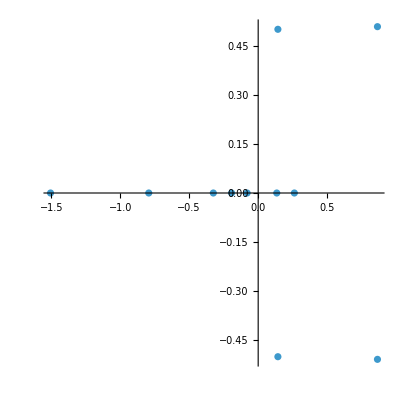

```mathematica
(*Mode numbers of the exact solution*)
branchchoice=0;
rootsExact=rootsfromcoeff[SYTlist[[λTchoice]]//ToYD,exactsol[[λTchoice,-1]]]/.(x[i_,j_,k_]->n_):>If[j==0,x[i,j,k]->n,Nothing]; (*-Pi might work better*)
CountingFunctionString[rigged[[2]],rigged[[1,1]]//Length]/.x[a_,b_]:>x[a,0,b]/.(rootsExact//StringSorter//Flatten)//Chop//N//Round[#,0.01]&
CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length]/.x[a_,b_]:>x[a,0,b]/.(rootsExact//StringSorter//Flatten)//Chop//N

(rootsExact/.(x[i_,j_,k_]->n_):>If[i==1,x[i,j,k]->n,Nothing]//Values)//ComplexListPlot[#,AspectRatio->1,PlotRange->All]&
```

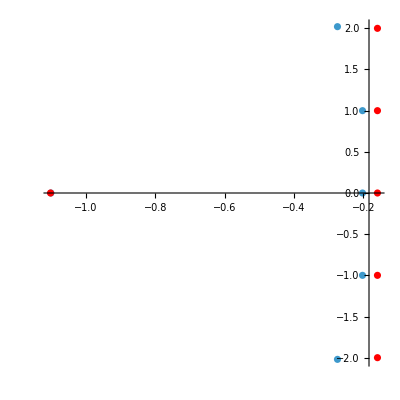

```mathematica
Show[(rootsExact/.(x[i_,j_,k_]->n_):>If[i==1,x[i,j,k]->n,Nothing]//Values)//ComplexListPlot[#,AspectRatio->1,PlotRange->All]&,-(BetheRootsFromStrings[rigged[[2]]]/.(x[i_,j_]->n_):>If[i==1,x[i,j]->n,Nothing]/.sol[1]//Values)//ComplexListPlot[#,AspectRatio->1,PlotStyle->Red]&,PlotRange->All]
```

```mathematica
(*Testing Zuxian's data*)
```

```mathematica
datatest=(Import["/Users/thomasscheutz/Documents/UU project on Bethe Ansatz/sub_{7,6}_{5,1}.csv"]//ToExpression)/.i->I;
```

branch cut

0

string mode numbers

{{-0.5,-4.5}}

exact mode numbers

{{-0.5,-4.5}}

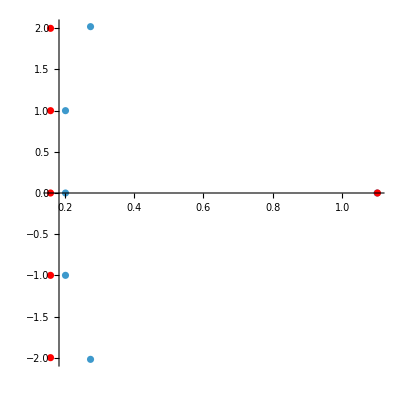

```mathematica
n=20;
rootsExact=Table[x[1,0,i]->datatest[[n,2,i]],{i,Length[datatest[[n,2]]]}];
SYT=datatest[[n,1]];

rigged=SYT//ToRiggedExact[#]&;
SolutionFromModeConfiguration[modes=(rigged//RiggedToModes),rigged[[1,1]]//Length];

Print["branch cut"]
branchchoice=0

Print["string mode numbers"]
CountingFunctionString[rigged[[2]],rigged[[1,1]]//Length]/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//N//Chop
(*CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length]/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//N//Chop
*)
Print["exact mode numbers"]
CountingFunctionString[rigged[[2]],rigged[[1,1]]//Length]/.x[a_,b_]:>x[a,0,b]/.(rootsExact//StringSorter//Flatten)//Chop//N
(*CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length]/.x[a_,b_]:>x[a,0,b]/.(rootsExact//StringSorter//Flatten)//Chop//N*)

Show[(rootsExact/.(x[i_,j_,k_]->n_):>If[i==1,x[i,j,k]->n,Nothing]//Values)//ComplexListPlot[#,AspectRatio->1,PlotRange->All]&,-(BetheRootsFromStrings[rigged[[2]]]/.(x[i_,j_]->n_):>If[i==1,x[i,j]->n,Nothing]/.sol[1]//Values)//ComplexListPlot[#,AspectRatio->1,PlotStyle->Red]&,PlotRange->All]
```

{x[1,0,1]→-0.543524+2.03134 ⅈ,x[1,0,2]→-0.430226+1.00003 ⅈ,x[1,0,3]→-0.430251,x[1,0,4]→-0.430226-1.00003 ⅈ,x[1,0,5]→-0.543524-2.03134 ⅈ,x[1,0,6]→0.0754731}

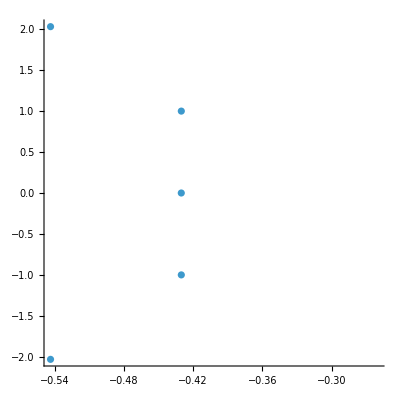

```mathematica
(*illustrating problem with nr 3*)
rootsExact//StringSorter//Flatten
%//Values//ComplexListPlot[#,AspectRatio->1]&
```

```mathematica
(*illustrating problem with nr 5*)

Table[branchchoice=i;
{CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length]/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//N//Chop,
CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length]/.x[a_,b_]:>x[a,0,b]/.(rootsExact//StringSorter//Flatten)//Chop//N},{i,-Pi,Pi,Pi/20}];

branchchoice=0;
testFunc=(*(ⅈ/2+x[1,6])/(-ⅈ/2+x[1,6])*)Table[CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length][[1,2,i]],{i,Length[CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length][[1,2]]]}]

testFunc/.x[a_,b_]:>x[a,0,b]/.(rootsExact//StringSorter//Flatten)//N
testFunc/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//N//Chop
```

{-5/2,-13 (-1/2+(ⅈ (ⅈ (-π+Arg[-(ⅈ/2+x[1,6])/(-ⅈ/2+x[1,6])])+Log[Abs[(ⅈ/2+x[1,6])/(-ⅈ/2+x[1,6])]]))/(2 π)),(ⅈ (ⅈ (-π+Arg[-(ⅈ-x[1,1]+x[1,6])/(-ⅈ-x[1,1]+x[1,6])])+Log[Abs[(ⅈ-x[1,1]+x[1,6])/(-ⅈ-x[1,1]+x[1,6])]]))/(2 π),(ⅈ (ⅈ (-π+Arg[-(ⅈ-x[1,2]+x[1,6])/(-ⅈ-x[1,2]+x[1,6])])+Log[Abs[(ⅈ-x[1,2]+x[1,6])/(-ⅈ-x[1,2]+x[1,6])]]))/(2 π),(ⅈ (ⅈ (-π+Arg[-(ⅈ-x[1,3]+x[1,6])/(-ⅈ-x[1,3]+x[1,6])])+Log[Abs[(ⅈ-x[1,3]+x[1,6])/(-ⅈ-x[1,3]+x[1,6])]]))/(2 π),(ⅈ (ⅈ (-π+Arg[-(ⅈ-x[1,4]+x[1,6])/(-ⅈ-x[1,4]+x[1,6])])+Log[Abs[(ⅈ-x[1,4]+x[1,6])/(-ⅈ-x[1,4]+x[1,6])]]))/(2 π),(ⅈ (ⅈ (-π+Arg[-(ⅈ-x[1,5]+x[1,6])/(-ⅈ-x[1,5]+x[1,6])])+Log[Abs[(ⅈ-x[1,5]+x[1,6])/(-ⅈ-x[1,5]+x[1,6])]]))/(2 π)}

{-2.5,-0.61994+2.29707×10^-16 ⅈ,0.946026-0.150361 ⅈ,0.789425-0.223766 ⅈ,0.649038+0. ⅈ,0.789425+0.223766 ⅈ,0.946026+0.150361 ⅈ}

{-2.5,0.420511,0.969343-0.168729 ⅈ,0.773807-0.302972 ⅈ,0.593188,0.773807+0.302972 ⅈ,0.969343+0.168729 ⅈ}

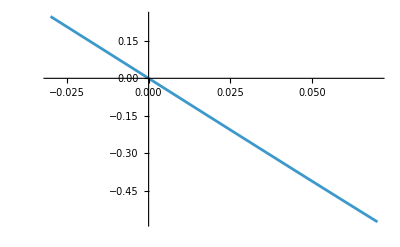

```mathematica
Plot[ 13(log[((ⅈ/2+x)/(-ⅈ/2+x)),0,0]/(2Pi I)-1/2)//Evaluate,{x,-0.03,0.07}]
```

```mathematica
testFunc/.x[1,6]->val/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//Total
```

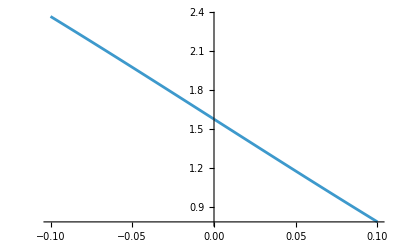

```mathematica
Plot[testFunc/.x[1,6]->val/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//Total//Evaluate,{val,-0.1,0.1}]
```

```mathematica
ⅈ/2+x=b I(-ⅈ/2+x)
```

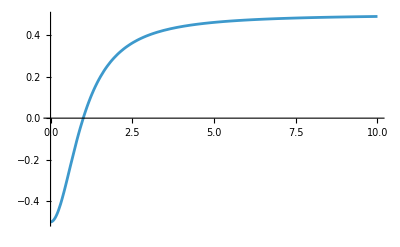

```mathematica
ComplexPlot3D[-I/2(b I+1)/(1-b I)//Im,{b,0,10},PlotRange->All]
```

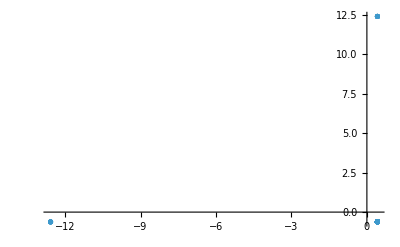

```mathematica
Table[branchchoice=i;
{Table[CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length][[1,2,i]],{i,Length[CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length][[1,2]]]}][[2]]/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//N//Chop,
Table[CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length][[1,2,i]],{i,Length[CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length][[1,2]]]}][[2]]/.x[a_,b_]:>x[a,0,b]/.(rootsExact//StringSorter//Flatten)//Chop//N},{i,-Pi,Pi,Pi/100}]//ListPlot
```

```mathematica
(*Finding problems*)
```

```mathematica
δ=10^-5I;
testRoots={x[1,1]->-0.35758732888587473050507467034133402874246320176079090905`40.+ⅈ/2+δ,x[1,2]->-0.35758732888587473050507467034133402874246320176079090905`40.-ⅈ/2-+δ,x[1,3]->-0.0910781085936275815114289414311317488954400034297166780221`40.,x[2,1]->-0.1799145153577099645093108510678658421777810695400747550313`40.};
```

```mathematica
branchchoice=RandomReal[{-Pi,Pi}];
CountingFunction[rigged[[2]],rigged[[1,1]]//Length]/.testRoots//Round[#,0.1]&
```

{{0.5,0.5},{0.}}

```mathematica
branchchoice=0;
Table[CountingFunction[rigged[[2]],rigged[[1,1]]//Length][[1,1,i]],{i,Length[CountingFunction[rigged[[2]],rigged[[1,1]]//Length][[1,1]]]}]/.x[a_,b_]:>x[a,0,b]/.(rootsExact//StringSorter//Flatten)

Table[CountingFunction[rigged[[2]],rigged[[1,1]]//Length][[1,1,i]],{i,Length[CountingFunction[rigged[[2]],rigged[[1,1]]//Length][[1,1]]]}]/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]
```

{-7/2,0.64979859541717002032407875941616724645+0. ⅈ,-2.9965581326942043420290205528901650902+0. ⅈ,0.444890855711483424936641012735500283438+0. ⅈ,0.34597978890666516743632899691402872986+0. ⅈ,-0.44528073223624718573742134513908375941+0. ⅈ,-0.99883037510486696863085820750679225383+0. ⅈ}

{-7/2,0.65588021410909339192922449372364055003+0. ⅈ,3,0.4440290659845052134115861608011954438009+0. ⅈ,0.34411978589090660807077550627635944997+0. ⅈ,-0.4440290659845052134115861608011954438009+0. ⅈ,0}

```mathematica
branchchoice=0;
CountingFunction[rigged[[2]],rigged[[1,1]]//Length][[1,1,-1]]
```

-(ⅈ (ⅈ (-π+Arg[-(ⅈ/2+x[1,2]-x[2,1])/(-ⅈ/2+x[1,1]-x[2,1])])+Log[Abs[(ⅈ/2+x[1,2]-x[2,1])/(-ⅈ/2+x[1,1]-x[2,1])]]))/(2 π)

-6 (-1/2+(ⅈ (ⅈ (-π+Arg[-(-ⅈ ϵ+v[1,2,1])/(ⅈ ϵ+v[1,2,1])])+Log[Abs[(-ⅈ ϵ+v[1,2,1])/(ⅈ ϵ+v[1,2,1])]]))/(2 π))

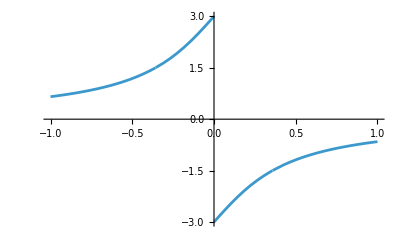

```mathematica
-6 (-1/2+(ⅈ (ⅈ (-π+Arg[-(ⅈ/2+x[1,2])/(-ⅈ/2+x[1,1])])+Log[Abs[(ⅈ/2+x[1,2])/(-ⅈ/2+x[1,1])]]))/(2 π))/.{x[1,1]->ⅈ/2+v[1,2,1]+I ϵ,x[1,2]->-ⅈ/2+v[1,2,1]-I ϵ,x[1,3]->v[1,1,1],x[2,1]->v[2,1,1]}
Plot[-6 (-1/2+(ⅈ (ⅈ (-π+Arg[-(ⅈ/2+x[1,2])/(-ⅈ/2+x[1,1])])+Log[Abs[(ⅈ/2+x[1,2])/(-ⅈ/2+x[1,1])]]))/(2 π))/.{x[1,1]->ⅈ/2+v[1,2,1]+I ϵ,x[1,2]->-ⅈ/2+v[1,2,1]-I ϵ,x[1,3]->v[1,1,1],x[2,1]->v[2,1,1]}/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//Evaluate,{ϵ,-1,1}]
```

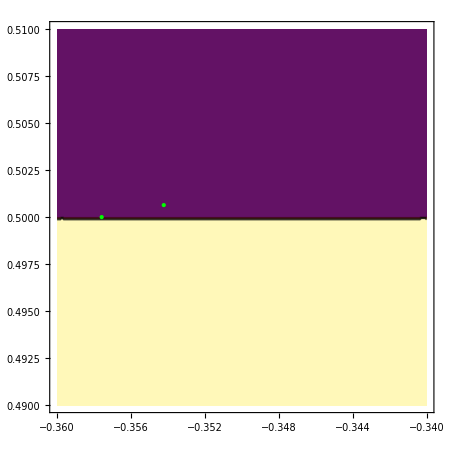

```mathematica
ContourPlot[-6 (-1/2+(ⅈ (ⅈ (-π+Arg[-(ⅈ/2+x[1,2])/(-ⅈ/2+x[1,1])])+Log[Abs[(ⅈ/2+x[1,2])/(-ⅈ/2+x[1,1])]]))/(2 π))/.x[1,1]->reval+I imval/.x[1,2]->reval-I imval//Re,{reval,-0.36,-0.34},{imval,0.49,0.51},Epilog->{PointSize[Medium],Green,{Point[{x[1,0,1]/.(rootsExact//StringSorter//Flatten)//Re,x[1,0,1]/.(rootsExact//StringSorter//Flatten)//Im}],Point[{x[1,1]/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//Re,x[1,1]/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//Im}]}}]
```

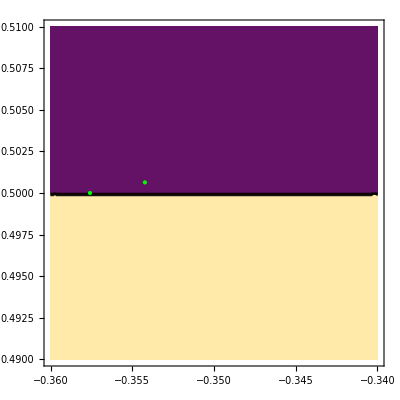

```mathematica
imval1=x[1,0,1]/.(rootsExact//StringSorter//Flatten)//Im;
imval2=x[1,0,2]/.(rootsExact//StringSorter//Flatten)//Im;
ContourPlot[-(ⅈ (ⅈ (-π+Arg[-(ⅈ/2+x[1,2]-x[2,1])/(-ⅈ/2+x[1,1]-x[2,1])])+Log[Abs[(ⅈ/2+x[1,2]-x[2,1])/(-ⅈ/2+x[1,1]-x[2,1])]]))/(2 π)/.x[1,1]->reval+I imval/.x[1,2]->reval-I imval/.x[2,1]->x[2,0,1]/.(rootsExact//StringSorter//Flatten)//Re,{reval,-0.36,-0.34},{imval,.49,.51},Epilog->{PointSize[Medium],Green,{Point[{x[1,0,1]/.(rootsExact//StringSorter//Flatten)//Re,x[1,0,1]/.(rootsExact//StringSorter//Flatten)//Im}],Point[{x[1,1]/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//Re,x[1,1]/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//Im}]}}]
```

```mathematica
(ⅈ (ⅈ (-π+Arg[-(ⅈ/2+x[1,2]-x[2,1])/(-ⅈ/2+x[1,1]-x[2,1])])+Log[Abs[(ⅈ/2+x[1,2]-x[2,1])/(-ⅈ/2+x[1,1]-x[2,1])]]))/(2 π)/.{x[1,1]->ⅈ/2+v[1,2,1]+I ϵ,x[1,2]->-ⅈ/2+v[1,2,1]-I ϵ,x[1,3]->v[1,1,1],x[2,1]->v[2,1,1]}
```

(ⅈ (ⅈ (-π+Arg[-(-ⅈ ϵ+v[1,2,1]-v[2,1,1])/(ⅈ ϵ+v[1,2,1]-v[2,1,1])])+Log[Abs[(-ⅈ ϵ+v[1,2,1]-v[2,1,1])/(ⅈ ϵ+v[1,2,1]-v[2,1,1])]]))/(2 π)

0

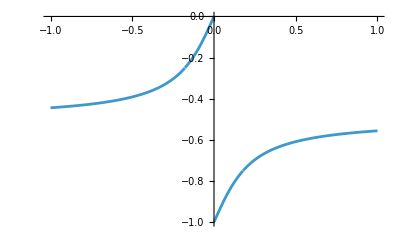

```mathematica
-(ⅈ (ⅈ (-π+Arg[-(ⅈ/2+x[1,2]-x[2,1])/(-ⅈ/2+x[1,1]-x[2,1])])+Log[Abs[(ⅈ/2+x[1,2]-x[2,1])/(-ⅈ/2+x[1,1]-x[2,1])]]))/(2 π)/.{x[1,1]->ⅈ/2+v[1,2,1]+I ϵ,x[1,2]->-ⅈ/2+v[1,2,1]-I ϵ,x[1,3]->v[1,1,1],x[2,1]->v[2,1,1]}/.ϵ->0
Plot[-(ⅈ (ⅈ (-π+Arg[-(ⅈ/2+x[1,2]-x[2,1])/(-ⅈ/2+x[1,1]-x[2,1])])+Log[Abs[(ⅈ/2+x[1,2]-x[2,1])/(-ⅈ/2+x[1,1]-x[2,1])]]))/(2 π)/.{x[1,1]->ⅈ/2+v[1,2,1]+I ϵ,x[1,2]->-ⅈ/2+v[1,2,1]-I ϵ,x[1,3]->v[1,1,1],x[2,1]->v[2,1,1]}/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//Evaluate,{ϵ,-10,10}]
```

```mathematica
-(ⅈ (ⅈ (-π+Arg[-(ⅈ/2+x[1,2]-x[2,1])/(-ⅈ/2+x[1,1]-x[2,1])])+Log[Abs[(ⅈ/2+x[1,2]-x[2,1])/(-ⅈ/2+x[1,1]-x[2,1])]]))/(2 π)/.{x[1,1]->ⅈ/2+v[1,2,1]+I ϵ,x[1,2]->-ⅈ/2+v[1,2,1]-I ϵ,x[1,3]->v[1,1,1],x[2,1]->v[2,1,1]}
```

-(ⅈ (ⅈ (-π+Arg[-(-ⅈ ϵ+v[1,2,1]-v[2,1,1])/(ⅈ ϵ+v[1,2,1]-v[2,1,1])])+Log[Abs[(-ⅈ ϵ+v[1,2,1]-v[2,1,1])/(ⅈ ϵ+v[1,2,1]-v[2,1,1])]]))/(2 π)

```mathematica
Clear[x,ϵ]
```

```mathematica
ϵ=Im[x[1,2-x[2,1]]]+I
x=Re[x[1,2-x[2,1]]]
```

```mathematica
-(x[1,1]-x[1,2]-I)/2I/.{x[1,1]->ⅈ/2+v[1,2,1]+I ϵ,x[1,2]->-ⅈ/2+v[1,2,1]-I ϵ}
```

ϵ

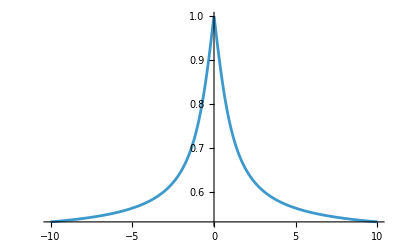

```mathematica
Plot[If[ϵ<0,log[(I ϵ+x)/(-I ϵ+x),0,0],log[(-I ϵ+x)/(I ϵ+x),0,0]]/(2Pi I)/.x->1//Evaluate,{ϵ,-10,10},PlotRange->All]
```

```mathematica
Manipulate[Show[Plot[log[(ⅈ ϵ+val)/(-ⅈ ϵ+val),-1,branch]/(2Pi I)/.ϵ->1//Re//Evaluate,{val,-10,10},PlotRange->All],Plot[log[(ⅈ ϵ+val)/(-ⅈ ϵ+val),-1,branch]/(2Pi I)/.val->1//Re//Evaluate,{ϵ,-10,10},PlotStyle->Red,PlotRange->All]],{branch,-Pi,Pi}]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

```mathematica
ComplexPlot3D[log[(v+I)/(v-I),-1,-Pi],{v,-10-10I,10+10I}]
```

-Graphics3D-

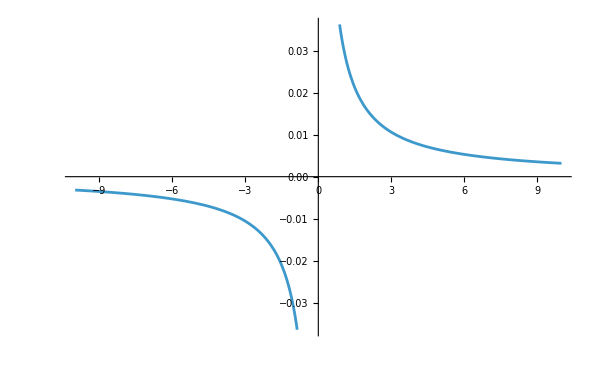

```mathematica
Plot[1/(2Pi I) log[(u-v+I ϵ)/(u-v-I ϵ),0,0]-(HeavisideTheta[ϵ]-Sign[ϵ]HeavisideTheta[u-v])/.v->0/.ϵ->.1//Re//Evaluate,{u,-10,10}]
```

#### Example cases

```mathematica
(*{{{1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{2,2,2,1,1},{2,2,1},{2},{}},{{0,0,1,0,2},{0,0,0},{1},{}}} does not work for CountingFunctionString or CountingFunctionKS*)
```

```mathematica
(*{{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{3,3,2,1,1},{2,2,1},{2},{}},{{1,1,2,1,1},{0,0,0},{1},{}}} 

{{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{2,2,1,1,1,1,1,1},{2,2,1},{2},{}},{{1,1,0,2,2,2,2,3},{1,1,1},{0},{}}}

{{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{3,2,1,1,1,1,1},{3,2},{2},{}},{{1,2,0,0,0,0,1},{2,0},{0},{}}} looks odd pictorially. Breaking KKR?

gives different mode numbers with the new counting function*)
```

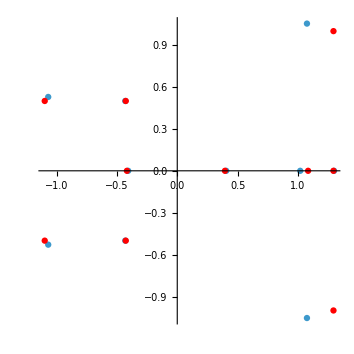
```mathematica
(*Problem: {{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{3,2,2,1,1,1},{3,2,1},{3},{}},{{2,0,0,1,6,7},{1,1,1},{0},{}}} for both counting functions
-Graphics-*)

(*Works if one chooses strings manually as*)
rootsTEST={x[1,0,1]->1.0740201528906787581498012546194698386101894154020423139156`36.71024402793401+1.054022117323437035095263975428082706034724338448164022037`36.702081321495406 ⅈ,x[1,0,10]->1.0183665997676829225831758867892306123538755146985665549112`36.31184701277256,x[1,0,3]->1.0740201528906787581498012546194698386101894154020423139156`36.71024402793401-1.054022117323437035095263975428082706034724338448164022037`36.702081321495406 ⅈ,x[1,0,4]->-1.0686705014856402462770144132902878815911852448271814123894`36.6558700178789+0.5287113551905657615256141850614132414485799909963626415762`36.35024483404912 ⅈ,x[1,0,5]->-1.0686705014856402462770144132902878815911852448271814123894`36.6558700178789-0.5287113551905657615256141850614132414485799909963626415762`36.35024483404912 ⅈ,x[1,0,6]->-0.4305429189005419591768779058730152626805497697012579664082`36.14701022585318+0.5000025421743976022996327690618956991786529833349847550912`36.21196598746346 ⅈ,x[1,0,7]->-0.4305429189005419591768779058730152626805497697012579664082`36.14701022585318-0.5000025421743976022996327690618956991786529833349847550912`36.21196598746346 ⅈ,x[1,0,8]->-0.4061842458823624573378871749516792651350298915063951471094`36.4483001003233,x[1,0,9]->0.4054444095426187399519386386847393866039396616131631705153`36.586664363045664,x[1,0,2]->1.2984978429159071634891401304412969679442349499057928847802`36.48074150200739,x[2,0,1]->0.8049578500580483354596655017651812715867221380785724368728`37.75383027496054+1.1333843500962776009594859717930144077024914459935731290025`37.902434346481535 ⅈ,x[2,0,2]->0.6957595114105177056314761381021626075253923674715867306452`37.80877418677506,x[2,0,3]->0.8049578500580483354596655017651812715867221380785724368728`37.75383027496054-1.1333843500962776009594859717930144077024914459935731290025`37.902434346481535 ⅈ,x[2,0,4]->-0.5157570762499377587523928102848337426944101071040070585907`38.01756003621882+0.4839906031240019421585013330399914227656170860395054019486`37.98995177068037 ⅈ,x[2,0,5]->-0.5157570762499377587523928102848337426944101071040070585907`38.01756003621882-0.4839906031240019421585013330399914227656170860395054019486`37.98995177068037 ⅈ,x[2,0,6]->1.1892297061675037452063732915843956096075861096417825127907`37.91591922328735,x[3,0,1]->0.2614065057166762983824190419206344823373052519461713510769`38.42769321630694+1.0063029837225749695127991133060272736357069279062859223906`39.01310558487634 ⅈ,x[3,0,2]->0.7088823711637687053613593224823576727841907656389072978466`39.225005543789095,x[3,0,3]->0.2614065057166762983824190419206344823373052519461713510769`38.42769321630694-1.0063029837225749695127991133060272736357069279062859223906`39.01310558487634 ⅈ};
```

```mathematica
(*Problem case: {{{1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{2,2,2,1,1},{2,2,1},{2},{}},{{0,0,1,0,2},{0,0,0},{1},{}}} WRONG RIGGED, for CountingFunctionKS and seemingly is not a problem of being close to branch cut

-Graphics-*)

Table[CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length][[1,4,i]],{i,Length[CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length][[1,4]]]}]/.x[a_,b_]:>x[a,0,b]/.(rootsExact//StringSorter//Flatten)//N

Table[CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length][[1,4,i]],{i,Length[CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length][[1,4]]]}]/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//N

{CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length][[1,4]][[-5]],CountingFunctionKS[rigged[[2]],rigged[[1,1]]//Length][[1,4]][[-4]]}

(ⅈ/2+x[1,7]-x[2,1])/(-ⅈ/2+x[1,7]-x[2,1])/.x[a_,b_]:>x[a,0,b]/.(rootsExact//StringSorter//Flatten)//N
(ⅈ/2+x[1,7]-x[2,1])/(-ⅈ/2+x[1,7]-x[2,1])/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]

(ⅈ/2+x[1,7]-x[2,2])/(-ⅈ/2+x[1,7]-x[2,2])/.x[a_,b_]:>x[a,0,b]/.(rootsExact//StringSorter//Flatten)//N
(ⅈ/2+x[1,7]-x[2,2])/(-ⅈ/2+x[1,7]-x[2,2])/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]

{x[1,7],x[2,2]}/.BetheRootsFromStrings[rigged[[2]]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]
{x[1,7],x[2,2]}/.x[a_,b_]:>x[a,0,b]/.(rootsExact//StringSorter//Flatten)
```

{-1.,4.62103+0. ⅈ,0.541855-0.178917 ⅈ,0.541855+0.178917 ⅈ,0.309061-0.120508 ⅈ,0.309061+0.120508 ⅈ,0.193796-0.0558551 ⅈ,0.193796+0.0558551 ⅈ,0.290971+0. ⅈ,-0.267126+0.360885 ⅈ,-0.267126-0.360885 ⅈ,-0.104923+0.0436806 ⅈ,-0.104923-0.0436806 ⅈ,-0.257323+0. ⅈ}

{-1.,4.41799+0. ⅈ,0.615701-0.154114 ⅈ,0.615701+0.154114 ⅈ,0.332138-0.132178 ⅈ,0.332138+0.132178 ⅈ,0.200069-0.0592158 ⅈ,0.200069+0.0592158 ⅈ,0.308428+0. ⅈ,-0.765546+0.370458 ⅈ,-0.765546-0.370458 ⅈ,-0.108613+0.0403544 ⅈ,-0.108613-0.0403544 ⅈ,-0.273913+0. ⅈ}

{-(ⅈ (ⅈ (-π+Arg[-(ⅈ/2+x[1,7]-x[2,1])/(-ⅈ/2+x[1,7]-x[2,1])])+Log[Abs[(ⅈ/2+x[1,7]-x[2,1])/(-ⅈ/2+x[1,7]-x[2,1])]]))/(2 π),-(ⅈ (ⅈ (-π+Arg[-(ⅈ/2+x[1,7]-x[2,2])/(-ⅈ/2+x[1,7]-x[2,2])])+Log[Abs[(ⅈ/2+x[1,7]-x[2,2])/(-ⅈ/2+x[1,7]-x[2,2])]]))/(2 π)}

-0.0111229-0.102971 ⅈ

0.0095109360984322343288973060944406482583+0.097059147909734778163220125363893296856 ⅈ

-1.03693-9.59946 ⅈ

1.+10.205004734048611078219946662237374355 ⅈ

{-0.7641581112796564320950116570720707182945,-0.8621492466157859631109954099712926534943-ⅈ/2}

{-0.84589806970953325813612327288786742,-0.7462138647059826096566278028936720472-0.4788477400142470546444014496918353163 ⅈ}

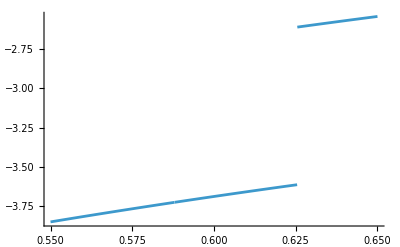

x[1,10]→0.6066845497005279898796528613311635206527

{x[1,0,10]→0.61211901679299105159149555482318856}

3.9653096065346495154371634495064583+0. ⅈ

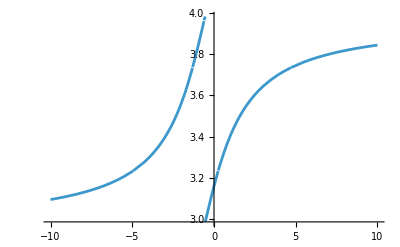

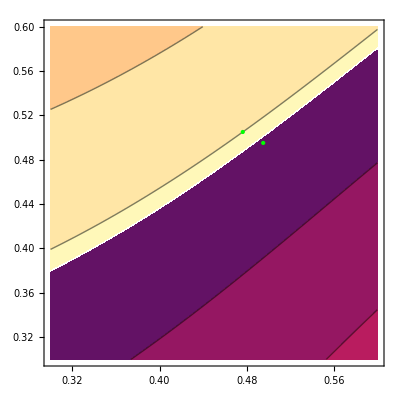

```mathematica
(*Problem case: {{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{4,2,1,1,1,1},{4,1,1},{2},{}},{{1,1,4,5,5,5},{0,0,1},{0},{}}} and choose log[x,0,-Pi] but not log[x,-1,0]*)
Plot[Allrelfused[[1,6]]/(2Pi I)/.x[1,10]->-val/.stringToXroots/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]//Evaluate,{val,0.55,0.65}]
stringToXroots[[10]]/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]
StringSorter[rootsExact][[1,-1]]

(*So appears not to be the above, as the discontinuity does not happen between the string and exact root*)

(*Problem appears to be the 4-string*)
Allrelfused[[1,6]]/(2Pi I)/.(StringSorter[rootsExact][[1,-6]]/.x[a_,b_,c_]:>x[a,c])/.stringToXroots/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]

(*This is difficult to see from the counting function*)

Plot[Allrelfused[[1,6]]/(2Pi I)/.stringToXroots/.v[a_,s_,k_]:>-v[a,s,k]/.v[1,4,1]->val/.sol[1]//Re//Evaluate,{val,-10,10}]

(*But can potentially be seen as follows:*)
val1Im=StringSorter[rootsExact][[1,-6]][[1]][[2]]//Im;
val2Im=StringSorter[rootsExact][[1,-6]][[2]][[2]]//Im;
ContourPlot[Allrelfused[[1,6]]/(2Pi I)/.x[1,1]->val1-I val1Im/.x[1,4]->val1+I val1Im/.x[1,2]->val2-I val2Im/.x[1,3]->val2+I val2Im/.(StringSorter[rootsExact]/.x[a_,b_,c_]:>x[a,c]//Flatten)//Evaluate,{val1,0.3,0.6},{val2,0.3,0.6},Epilog->{PointSize[Medium],Green,{Point[{StringSorter[rootsExact][[1,-6]][[1]][[2]]//Re,StringSorter[rootsExact][[1,-6]][[2]][[2]]//Re}],Point[{-v[1,4,1]/.sol[1],-v[1,4,1]/.sol[1]}]}}]
```

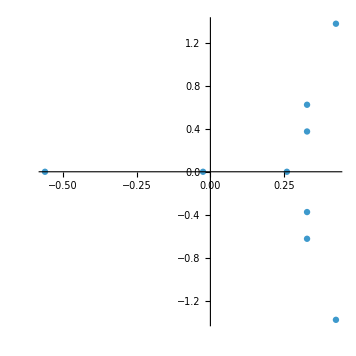
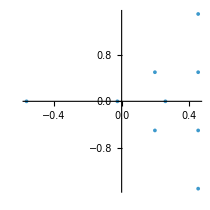
```mathematica
(*Problem case:{{{1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{4,2,1,1,1},{4,1},{1},{}},{{1,2,1,3,4},{0,1},{0},{}}} and choose log[x,.,0] or log[x,.,-Pi] or any log[x,.,RandomReal[]Pi]*) (*IT WORKS FOR CountingFunctionKS at branch on 0 but not -Pi as CountingFunctionKS[[1,1,18]] goes to negative real axis for the exact solution*)

(*As it does not seem to work for any branch cut, it seems to me likely that the problem is not fictitious*)

(*Observe that the string sorting function does likely not give appropriate result, as the roots are too close -Graphics-. Look at the following instead (where I have changed what roots are parts of what strings):*)
exacttest={{{x[1,0,1]->0.4264705583669233201064265735313160257739039780090240737104`35.52737083141202+1.3798467379709689407513425278444307594862820441688994985599`36.0373126278558 ⅈ,x[1,0,4]->0.4264705583669233201064265735313160257739039780090240737104`35.52737083141202-1.3798467379709689407513425278444307594862820441688994985599`36.0373126278558 ⅈ,x[1,0,2]->0.3283035150193460458008142657205330908774772039809153933053`35.47291885878611+0.6245269610763028663083497875527645332543481520325249363107`35.75219451798773 ⅈ,x[1,0,3]->0.3283035150193460458008142657205330908774772039809153933053`35.47291885878611-0.6245269610763028663083497875527645332543481520325249363107`35.75219451798773 ⅈ},{x[1,0,5]->0.328305493981878480105772094222210845982089380791260224287`35.1936873374724+0.3754706537377179708287584400243429060461226521460497719145`35.25198518585866 ⅈ,x[1,0,6]->0.328305493981878480105772094222210845982089380791260224287`35.1936873374724-0.3754706537377179708287584400243429060461226521460497719145`35.25198518585866 ⅈ},{x[1,0,7]->-0.5619866671625608784210845208852548239391922111131001816779`35.90660874848264},{x[1,0,8]->-0.0250264419169034328695055660883210642667441992154890301705`35.11744910697506},{x[1,0,9]->0.2597594674546208750423577163751150710301410386266634620577`35.50294715040426}},{{x[2,0,1]->0.2244840180342444815429921584764628083970367852151294967867`37.92431576521435+1.4305329234529361843428596392779757929773536113604596549408`38.72862819549779 ⅈ,x[2,0,2]->0.2568193168604828781165203252145973742270498054209278939831`38.14778804858631+0.4999922961256359320201290840216814032150105502091521497267`38.43712367495498 ⅈ,x[2,0,3]->0.2568193168604828781165203252145973742270498054209278939831`38.14778804858631-0.4999922961256359320201290840216814032150105502091521497267`38.43712367495498 ⅈ,x[2,0,4]->0.2244840180342444815429921584764628083970367852151294967867`37.92431576521435-1.4305329234529361843428596392779757929773536113604596549408`38.72862819549779 ⅈ},{x[2,0,5]->-0.0275940877756534674317388750696413519039002101188555041963`38.037757334412866}},{{x[3,0,1]->0.031119670916150247996778688275298918597400188446044921875`40.}}};

(*The problem are the 2-string and the 4-string*)
Allrelfused[[1,1;;2]]/(2Pi I)/.stringToXroots/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]
Allrelfused[[1,1;;2]]/(2Pi I)/.(exacttest[[1,-4]]/.x[a_,b_,c_]:>x[a,c])/.stringToXroots/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]
Allrelfused[[1,1;;2]]/(2Pi I)/.(exacttest[[1,-5]]/.x[a_,b_,c_]:>x[a,c])/.stringToXroots/.v[a_,s_,k_]:>-v[a,s,k]/.sol[1]

(*Is the example in fact a situation when the KKR bijection would fail? The string solution is quite different from the exact: -Graphics-*)

(*The problem seems not to be fictitious (at least not for 4-string, which seems to not be close to branch cut)*)

valIm0=exacttest[[1,-4]][[1]][[2]]//Im;
Manipulate[Plot[Allrelfused[[1,1]]/(2Pi I)/.x[1,5]->val+I valIm/.x[1,6]->val-I valIm/.(exacttest/.x[a_,b_,c_]:>x[a,c]//Flatten)//Re//Evaluate,{val,0,1},Epilog->{PointSize[Medium],Green,Point[{exacttest[[1,-4]][[1]][[2]]//Re,0}],Point[{-v[1,2,1]/.sol[1],0}]}],{valIm,valIm0,0.5I}]

val1Im0=exacttest[[1,-5]][[1]][[2]]//Im;
val2Im0=exacttest[[1,-5]][[3]][[2]]//Im;
Manipulate[ContourPlot[Allrelfused[[1,1]]/(2Pi I)/.x[1,1]->val1+I val1Im/.x[1,4]->val1-I val1Im/.x[1,2]->val2+I val2Im/.x[1,3]->val2-I val2Im/.(StringSorter[rootsExact]/.x[a_,b_,c_]:>x[a,c]//Flatten)//Evaluate,{val1,0,1},{val2,0,1},Epilog->{PointSize[Medium],Green,{Point[{StringSorter[rootsExact][[1,-5]][[1]][[2]]//Re,StringSorter[rootsExact][[1,-5]][[3]][[2]]//Re}],Point[{-v[1,4,1]/.sol[1],-v[1,4,1]/.sol[1]}]}}],{val1Im,val1Im0,1.5},{val2Im,0.5,val2Im0}]

(*Looking at SYT history, it seems the same problem arises only at the last step, if one randomises branchchoice.*)
```

{20.+0. ⅈ,20.+0. ⅈ}

{20.9008+0. ⅈ,20.1821+0. ⅈ}

{33.9304+0. ⅈ,20.0132+0. ⅈ}

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Arg::indet: Indeterminate expression Arg[ComplexInfinity] encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Part::partw: Part 3 of {x[1,0,6]→-0.186016223745957535652086796738465803} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Arg::indet: Indeterminate expression Arg[ComplexInfinity] encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Part::partw: Part 3 of {x[1,0,6]→-0.186016223745957535652086796738465803} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 3 of {x[1,0,6]→-0.1680648984019579161276305614698171} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Part::partw: Part 3 of {x[1,0,4]→-1.06867050148564024627701441329028788+0.528711355190565761525614185061413241 ⅈ,x[1,0,5]→-1.06867050148564024627701441329028788-0.528711355190565761525614185061413241 ⅈ} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Part::partw: Part 3 of {x[1,0,1]→-0.791902072115090006799468712420510246+0.505004342746622692600954323004235546 ⅈ,x[1,0,2]→-0.791902072115090006799468712420510246-0.505004342746622692600954323004235546 ⅈ} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

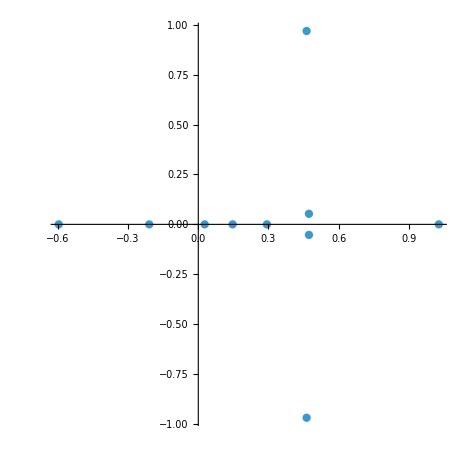
```mathematica
(*{{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{3,1,1,1,1,1,1,1},{2,2,1},{2},{}},{{1,1,2,3,3,3,3,3},{1,1,1},{1},{}}} has the same slight complexification of real roots, -Graphics-, but no mode number problem (for random branchchoice=-9.259193186589597)*)
```

#### Comparing with the method of Kirillov and Sakamoto 1509.02305

(relies on separating roots into strings; also, I find their bijection to rigged configurations hard to penetrate)

```mathematica
{12Log[((x1+I/2)/(x1-I/2))]-Log[(x1-x2+I)/(x1-x2-I)(x1-x3+I)/(x1-x3-I)(x1-x4+I)/(x1-x4-I)(x1-x5+I)/(x1-x5-I)(x1-x6+I)/(x1-x6-I)],
12Log[((x2+I/2)/(x2-I/2)(x3+I/2)/(x3-I/2))]-Log[(x2-x1+I)/(x2-x1-I)(x2-x4+I)/(x2-x4-I)(x2-x5+I)/(x2-x5-I)(x2-x6+I)/(x2-x6-I)(x3-x1+I)/(x3-x1-I)(x3-x4+I)/(x3-x4-I)(x3-x5+I)/(x3-x5-I)(x3-x6+I)/(x3-x6-I)],
12Log[((x4+I/2)/(x4-I/2)(x5+I/2)/(x5-I/2)(x6+I/2)/(x6-I/2))]-Log[(x4-x1+I)/(x4-x1-I)(x4-x2+I)/(x4-x2-I)(x4-x3+I)/(x4-x3-I)(x5-x1+I)/(x5-x1-I)(x5-x2+I)/(x5-x2-I)(x5-x3+I)/(x5-x3-I)(x6-x1+I)/(x6-x1-I)(x6-x2+I)/(x6-x2-I)(x6-x3+I)/(x6-x3-I)]}/(2Pi I)/.{x1->-.71532188,x2->-.45810568-.50017785I,x3->-.45810568+.50017785I,x4->.54241927,x5->.54241927+.99639165I,x6->.54241927-.99639165I}//Chop
```

{-1.99975,-3.99945,4.99654}

```mathematica
rigged={{lboxes={1,1,1,1,1,1,1,1,1,1,1,1}},{{3,2,1},{}},{{0,2,6},{}}};
rigged//showRC
SolutionFromModeConfiguration[modes=(rigged//RiggedToModes),L=lboxes//Length];
KirillovSakamotosoltest=sol[1];
```

-Graphics- | ∅

```mathematica
{12Log[((x1+I/2)/(x1-I/2))]-Log[(x1-x2+I)/(x1-x2-I)(x1-x3+I)/(x1-x3-I)(x1-x4+I)/(x1-x4-I)(x1-x5+I)/(x1-x5-I)(x1-x6+I)/(x1-x6-I)],
12Log[((x2+I/2)/(x2-I/2)(x3+I/2)/(x3-I/2))]-Log[(x2-x1+I)/(x2-x1-I)(x2-x4+I)/(x2-x4-I)(x2-x5+I)/(x2-x5-I)(x2-x6+I)/(x2-x6-I)(x3-x1+I)/(x3-x1-I)(x3-x4+I)/(x3-x4-I)(x3-x5+I)/(x3-x5-I)(x3-x6+I)/(x3-x6-I)],
12Log[((x4+I/2)/(x4-I/2)(x5+I/2)/(x5-I/2)(x6+I/2)/(x6-I/2))]-Log[(x4-x1+I)/(x4-x1-I)(x4-x2+I)/(x4-x2-I)(x4-x3+I)/(x4-x3-I)(x5-x1+I)/(x5-x1-I)(x5-x2+I)/(x5-x2-I)(x5-x3+I)/(x5-x3-I)(x6-x1+I)/(x6-x1-I)(x6-x2+I)/(x6-x2-I)(x6-x3+I)/(x6-x3-I)]}/(2Pi I)/.{x1->v[1,1,1],x2->v[1,2,1]-.5I,x3->v[1,2,1]+.5I,x4->v[1,3,1],x5->v[1,3,1]+I,x6->v[1,3,1]-I}/.KirillovSakamotosoltest
```

{-2.+3.53395×10^-17 ⅈ,-4.+3.53395×10^-17 ⅈ,5.+7.0679×10^-17 ⅈ}